```mathematica
pathtodirectory ="~/Desktop/";
```

## Style

```mathematica
labelfont = "Arial";
Clear[x];
prediction[x_]:=-6.367767314992545+4.6042335007240975 √x;
```

```mathematica
redtoblue[z_]:= Blend[{RGBColor[1,0,0], RGBColor[0,0,1]}, z];
bluetored[z_] := Blend[{RGBColor[0,0,1], RGBColor[1,0,0]}, z];
```

## Figure 2 : Time Series

```mathematica
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/large_unprocessed_data/fig2"];
```

```mathematica
skip = 10;
samplesize =500;
endtime = 10000/skip-1;
phenos= 20;
currentit = 2;
iterations = 1;
colorofplot[ z_ ] := Blend[{RGBColor[0.5,0.5,1], RGBColor[1,0.5,0] }, z];
thicknesstable = Table[{Directive[Thick, PointSize[Medium]], Directive[Thin], Directive[Thin]}];
thicknesslist = {Directive[Thick, PointSize[Medium]], Directive[Thick], Directive[Thick]};
```

```mathematica
scalerfreq=Table[{}, {it, 1, iterations}];
threshfreq=Table[{}, {it, 1, iterations}];
it = 1;
stat =Import["Context_STATISTICS_Dim020_Pop1000_Gen10000_B10.00_C1.00_PM1.0000_SM0.0010_ICthresh14.22300_ICscaler0.50000_Tsigma0.50000_Ssigma0.01000_invadingscaler0.00000_iteration"<>ToString[currentit]];
times = Drop[stat[[All,1]],1];
threshfreq[[it]] =Transpose[{times,Drop[stat[[All,4]],1]}];
scalerfreq[[it]] =Transpose[{times,Drop[stat[[All,5]],1]}];
```

### Export scalar frequency

```mathematica
averagedscalers =Table[scalerfreq[[i]][[All,2]],{i, 1, iterations}];
averagedscalers1=Transpose[{times,N[Mean[averagedscalers]]}];
totalscalerfreq= MovingAverage[averagedscalers1,100];
```

```mathematica
totalscalerfreq
```

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data"];
Export["fig2_plastic_frequencies.txt", Flatten[totalscalerfreq]];
SetDirectory[currentdir];
```

### Export Donations

```mathematica
donations = Drop[stat[[All,10]], 1];
```

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data"];
Export["fig2_donations.txt", Flatten[donations]];
Export["fig2_plastic_frequencies_unsmoothed.txt", Drop[stat[[All,5]],1]];
SetDirectory[currentdir];
```

### Export PhenoStd

```mathematica
allvars = Table[Sqrt[Drop[stat[[All,15+i*2]], 1]], {i, 0, 19}];
totalstddevs = Total[allvars];
```

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data"];
Export["fig2_total_pstd.txt", Flatten[totalstddevs]];
SetDirectory[currentdir];
```

### Export Thresholds

```mathematica
avgscaler = Drop[stat[[All,11]],1];
dpts=Table[{i, avgscaler[[i]]}, {i, 1, Length[avgscaler],50}];
dptslist ={#} &/@dpts;
dstyle1 = Table[{Opacity[Drop[stat[[All,5]],1][[i]]/1000],Blue}, {i, 1, Length[donations],50}];
frequencyC=Drop[stat[[All,5]],1]/1000;
```

```mathematica
avgthresh = Drop[stat[[All,6]],1];
tpts=Table[{i, avgthresh[[i]]}, {i, 1, Length[avgthresh],50}];
tptslist ={#} &/@tpts;
tstyle1 = Table[{Opacity[Drop[stat[[All,4]],1][[i]]/1000],Red}, {i, 1, Length[Drop[stat[[All,4]],1]],50}];
```

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data"];
Export["fig2_innate_thresh_value.txt", Flatten[tptslist]];
Export["fig2_innate_thresh_plotopacity.txt", Table[N[Drop[stat[[All,4]],1][[i]]/1000], {i, 1, Length[Drop[stat[[All,4]],1]],50}]];
SetDirectory[currentdir];
```

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data"];
Export["fig2_plastic_thresh_value.txt", Flatten[dptslist]];
Export["fig2_plastic_thresh_plotopacity.txt", Table[N[Drop[stat[[All,5]],1][[i]]/1000], {i, 1, Length[Drop[stat[[All,5]],1]],50}]];
SetDirectory[currentdir];
```

## Figure 3 : Optimal Thresh Fig

### Parameters

```mathematica
redtowhite[z_]:= Blend[{RGBColor[1,0,0],RGBColor[1,.9,.9]}, z]
whitetoblue[z_]:= Blend[{RGBColor[1,1,1],RGBColor[0,0,1]}, z]
labelfont="Arial";
```

```mathematica
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/large_unprocessed_data/fig3_optimalthresh"];
```

```mathematica
lowval = 150;
highval = 850;
```

### For plastic individuals:

#### Import simulation 1

```mathematica
data = Import["threshold_payoff_ranges_1.txt","CSV"];
```

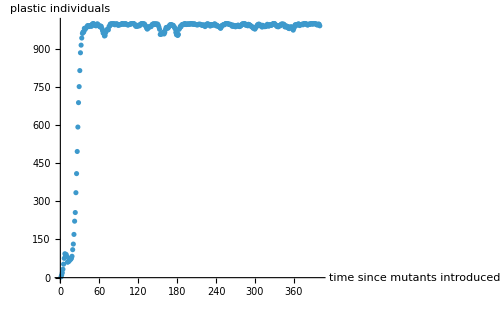

```mathematica
table1=Table[{i,Length[Flatten[Position[data[[i*1000+2;;( i)*1000+1000]][[All,4]],_?(#==-1&)]]]}, {i, 1, 400}];
ListPlot[table1, PlotRange->{All,All}, AxesLabel->{"time since mutants introduced","plastic individuals"}, ImageSize->500]
```

```mathematica
lowest=table1[[Flatten[Position[table1[[All,2]],Nearest[table1[[All,2]], lowval][[1]]]]]][[1]][[1]];
highest = table1[[Flatten[Position[table1[[All,2]],Nearest[table1[[All,2]], highval][[1]]]]]][[1]][[1]];
Print[lowest, " , ", highest]
```

20 , 31

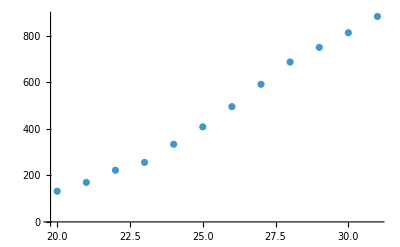

```mathematica
table1=Table[{i,Length[Flatten[Position[data[[i*1000+2;;( i)*1000+1000]][[All,4]],_?(#==-1&)]]]}, {i, lowest, highest}];
ListPlot[table1]
```

```mathematica
sumallelements={};
tt = lowest+10;
bottomtime=tt;
toptime=bottomtime+1;

allplastics=Flatten[Position[Drop[data,1][[All,4]][[bottomtime*1000+1;;toptime*1000]],-1]];

avgdists=Drop[data,1][[All,3]][[bottomtime*1000+1;;toptime*1000]][[allplastics]];
originalTP = Table[{Drop[data[[All,8+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allplastics]],Drop[data[[All,9+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allplastics]]}, {i, 0, 10}];
TP=Table[Transpose[originalTP[[i]]],{i, 1, 11}];
allcoordsbefore={};
```

```mathematica
For[i0 = 1, i0 <Length[TP[[1]]],i0++,
nonfloors=TP[[All,i0]][[All,1]];
partitions=BinCounts[nonfloors,{0,1001,1}];
dropempties=TakeList[nonfloors,partitions]/. {}->Nothing;
floor1=Map[Floor, Map[Mean,dropempties]];
deltaps=TakeList[TP[[All,i0]][[All,2]],partitions]/.{}-> Nothing;
deltap1=Map[Mean,deltaps];

floor1=floor1/. 0 -> 1;

inputnums=Table[0, {i, 1, 1001}];
inputnums[[1;;floor1[[1]]]] = deltap1[[1]];
For[i =1, i <Length[floor1],i++,
inputnums[[floor1[[i]];;floor1[[i+1]]]] = deltap1[[i+1]]
];
AppendTo[allcoordsbefore,Transpose[{Table[avgdists[[i0]],{k, 1, 1001}],Range[1,1001], inputnums}]];
];
```

```mathematica
densitylistbefore=allcoordsbefore;
densitylistbefore = Flatten[densitylistbefore,1];
```

```mathematica
TP[[All,i0]][[All,1]]
```

{13.8834,14.894,15.6636,17.4314,17.5061,17.6158,17.6916,18.8297,20.1163,21.5649,1000}

```mathematica
partitions=BinCounts[nonfloors,{0,1001,1}]
```

SparseArray[…]

```mathematica
Map[Floor, Map[Mean,dropempties]]
```

{14,15,16,17,19,20,21,1000}

```mathematica
dropempties
```

{{14.2968},{15.4331,15.7435},{16.1231,16.9875},{17.9153},{19.3339,19.7608},{20.1521},{21.3372},{1000}}

```mathematica
nonfloors=TP[[All,i0]][[All,1]];
partitions=BinCounts[nonfloors,{0,1001,1}];
dropempties=TakeList[nonfloors,partitions]/. {}->Nothing;
floor1=Map[Floor, Map[Mean,dropempties]];
deltaps=TakeList[TP[[All,i0]][[All,2]],partitions]/.{}-> Nothing;
deltap1=Map[Mean,deltaps];
```

```mathematica
dropempties=TakeList[nonfloors,partitions]/. {}->Nothing
floor1=Map[Floor, Map[Mean,dropempties]]
```

{{13.8834},{14.894},{15.6636},{17.4314,17.5061,17.6158,17.6916},{18.8297},{20.1163},{21.5649},{1000}}

{13,14,15,17,18,20,21,1000}

```mathematica
deltaps=TakeList[TP[[All,i0]][[All,2]],partitions]/.{}-> Nothing
deltap1=Map[Mean,deltaps]
```

{{0.},{0.066081},{0.132102},{0.198063,0.263965,-0.17382,-0.10781},{-0.041859},{-0.478911},{-0.915567},{-0.849341}}

{0.,0.066081,0.132102,0.0450995,-0.041859,-0.478911,-0.915567,-0.849341}

#### Bin the data (1)

```mathematica
sumallelements={};
For[tt = lowest,tt<=highest, tt++,
bottomtime=tt;
toptime=bottomtime+1;

allplastics=Flatten[Position[Drop[data,1][[All,4]][[bottomtime*1000+1;;toptime*1000]],-1]];

avgdists=Drop[data,1][[All,3]][[bottomtime*1000+1;;toptime*1000]][[allplastics]];
originalTP = Table[{Drop[data[[All,8+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allplastics]],Drop[data[[All,9+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allplastics]]}, {i, 0, 10}];
TP=Table[Transpose[originalTP[[i]]],{i, 1, 11}];
allcoordsbefore={};

For[i0 = 1, i0 <Length[TP[[1]]],i0++,
nonfloors=TP[[All,i0]][[All,1]];
partitions=BinCounts[nonfloors,{0,1001,1}];
dropempties=TakeList[nonfloors,partitions]/. {}->Nothing;
floor1=Map[Floor, Map[Mean,dropempties]];
deltaps=TakeList[TP[[All,i0]][[All,2]],partitions]/.{}-> Nothing;
deltap1=Map[Mean,deltaps];

floor1=floor1/. 0 -> 1;

inputnums=Table[0, {i, 1, 1001}];
inputnums[[1;;floor1[[1]]]] = deltap1[[1]];
For[i =1, i <Length[floor1],i++,
inputnums[[floor1[[i]];;floor1[[i+1]]]] = deltap1[[i+1]]
];
AppendTo[allcoordsbefore,Transpose[{Table[avgdists[[i0]],{k, 1, 1001}],Range[1,1001], inputnums}]];
];
densitylistbefore=allcoordsbefore;
densitylistbefore = Flatten[densitylistbefore,1];

maxdist = 50;
maxT = 50;
partitiongrid = 50;

list=Sort[densitylistbefore, #1[[1]]<#2[[1]]&];
partitions=BinCounts[list[[All,1]],maxdist/partitiongrid];
binnedcoords=TakeList[list,partitions];

binnedsublists = {};
For[i = 1, i ≤ Length[binnedcoords], i++,
list=Sort[binnedcoords[[i]], #1[[2]]<#2[[2]]&];
If[list ≠ {},
partitions=BinCounts[list[[All,2]],maxT/partitiongrid];
AppendTo[binnedsublists,TakeList[list,partitions]];
];
];

binnedsublistsbefore=binnedsublists;
totaldeltaP={};
mindeltaP={};
maxdeltaP={};
standarddevdeltaP={};

min=5;
max=50;
binnedsublists=binnedsublistsbefore;

For[i = 1, i <= Length[binnedsublists],i++,
For[j = 1, j<= Length[binnedsublists[[i]]],j++,
If[binnedsublists[[i]][[j]] != {},
If[Floor[binnedsublists[[i]][[j]][[1]][[1]]] <= max &&Floor[binnedsublists[[i]][[j]][[1]][[1]]] >= min,
AppendTo[totaldeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Total[binnedsublists[[i]][[j]][[All,3]]]}];
];
AppendTo[mindeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Min[binnedsublists[[i]][[j]][[All,3]]]}];
AppendTo[maxdeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Max[binnedsublists[[i]][[j]][[All,3]]]}];
]
]
];

totaldeltaPbefore=totaldeltaP;
standarddevdeltaPbefore=standarddevdeltaP;

maxbefore=Max[totaldeltaP[[All,3]]];
minbefore=Min[totaldeltaP[[All,3]]];

If[minbefore !=maxbefore,
mindensityb=minbefore;
maxdensityb=maxbefore;,
mindensityb = 0;
maxdensityb = 1;
];

If[maxdensityb==0,
maxdensityb=1;
d0b=-mindensityb/(maxdensityb-mindensityb),

];

d0b=-mindensityb/(maxdensityb-mindensityb);
piece1b[x_]:=d0b/(Log[-mindensityb+1])*Log[x-mindensityb+1];
piece2b[x_]:=((1-d0b)/(maxdensityb)^2)*x^2+d0b;
pwb[x_]:=Piecewise[{{piece1b[x], x < 0},{piece2b[x], x >=0} }];

delta=1;
deltad0=.003;

underlyingcolorbefore[z_]:=Map[Piecewise,{Join[Table[{redtowhite[i*(d0b-deltad0)/(18*(d0b-deltad0))],(i-1*delta)*d0b*.05<=z<i*d0b*.05},{i, 1, 18,delta}],{{RGBColor[1,.9,.9],18*d0b*.05<=z<d0b-deltad0*1.5},{RGBColor[1,.95,.95],d0b-deltad0*1.5<=z<d0b-deltad0},{RGBColor[1,1,1],(d0b-deltad0)<=z≤(d0b+deltad0)}},Table[{whitetoblue[(1-d0b-deltad0)*i/(18*(1-d0b-deltad0))],d0b+deltad0+(1-(d0b+deltad0))/18*(i-1)<z<=d0b+deltad0+(1-(d0b+deltad0))/18*(i)},{i, 1, 18,1}],{{RGBColor[0,0,1],1<z<100}}]}];

colordensityfunctionbefore[x_]:= underlyingcolorbefore[pwb[x]];
plotlegendbefore=BarLegend[{colordensityfunctionbefore,{mindensityb,maxdensityb}},LegendLabel->"Δ P", LabelStyle->Directive[Bold, Medium, Black,15]];

transformedcolorbefore=Table[underlyingcolorbefore[pwb[totaldeltaPbefore[[i]][[3]]]],{i, 1, Length[totaldeltaPbefore[[All,3]]]}];

AppendTo[sumallelements, totaldeltaPbefore];
]
```

```mathematica
sumallelements1plastic = sumallelements;
```

#### Import simulation 2

```mathematica
data = Import["threshold_payoff_ranges_2.txt","CSV"];
```

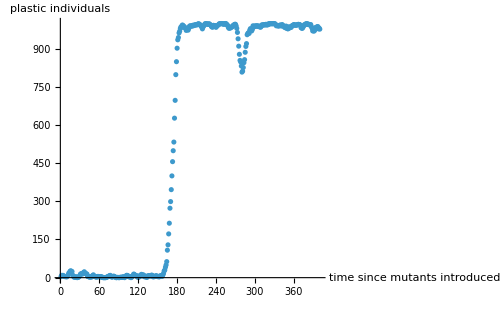

```mathematica
table1=Table[{i,Length[Flatten[Position[data[[i*1000+2;;( i)*1000+1000]][[All,4]],_?(#==-1&)]]]}, {i, 1, 400}];
ListPlot[table1, PlotRange->{All,All}, AxesLabel->{"time since mutants introduced","plastic individuals"}, ImageSize->500]
```

```mathematica
lowest=table1[[Flatten[Position[table1[[All,2]],Nearest[table1[[All,2]], lowval][[1]]]]]][[1]][[1]];
highest = table1[[Flatten[Position[table1[[All,2]],Nearest[table1[[All,2]], highval][[1]]]]]][[1]][[1]];
Print[lowest, " , ", highest]
```

166 , 179

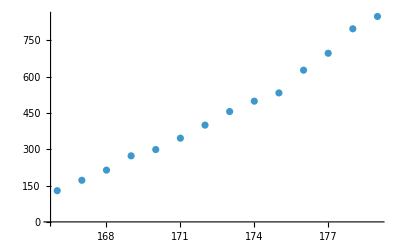

```mathematica
table1=Table[{i,Length[Flatten[Position[data[[i*1000+2;;( i)*1000+1000]][[All,4]],_?(#==-1&)]]]}, {i, lowest, highest}];
ListPlot[table1]
```

#### Bin the data (2)

```mathematica
sumallelements={};
For[tt = lowest,tt<=highest, tt++,
bottomtime=tt;
toptime=bottomtime+1;

allplastics=Flatten[Position[Drop[data,1][[All,4]][[bottomtime*1000+1;;toptime*1000]],-1]];

avgdists=Drop[data,1][[All,3]][[bottomtime*1000+1;;toptime*1000]][[allplastics]];
originalTP = Table[{Drop[data[[All,8+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allplastics]],Drop[data[[All,9+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allplastics]]}, {i, 0, 10}];
TP=Table[Transpose[originalTP[[i]]],{i, 1, 11}];
allcoordsbefore={};

For[i0 = 1, i0 <Length[TP[[1]]],i0++,
nonfloors=TP[[All,i0]][[All,1]];
partitions=BinCounts[nonfloors,{0,1001,1}];
dropempties=TakeList[nonfloors,partitions]/. {}->Nothing;
floor1=Map[Floor, Map[Mean,dropempties]];
deltaps=TakeList[TP[[All,i0]][[All,2]],partitions]/.{}-> Nothing;
deltap1=Map[Mean,deltaps];

floor1=floor1/. 0 -> 1;

inputnums=Table[0, {i, 1, 1001}];
inputnums[[1;;floor1[[1]]]] = deltap1[[1]];
For[i =1, i <Length[floor1],i++,
inputnums[[floor1[[i]];;floor1[[i+1]]]] = deltap1[[i+1]]
];
AppendTo[allcoordsbefore,Transpose[{Table[avgdists[[i0]],{k, 1, 1001}],Range[1,1001], inputnums}]];
];
densitylistbefore=allcoordsbefore;
densitylistbefore = Flatten[densitylistbefore,1];

maxdist = 50;
maxT = 50;
partitiongrid = 50;

list=Sort[densitylistbefore, #1[[1]]<#2[[1]]&];
partitions=BinCounts[list[[All,1]],maxdist/partitiongrid];
binnedcoords=TakeList[list,partitions];

binnedsublists = {};
For[i = 1, i ≤ Length[binnedcoords], i++,
list=Sort[binnedcoords[[i]], #1[[2]]<#2[[2]]&];
If[list ≠ {},
partitions=BinCounts[list[[All,2]],maxT/partitiongrid];
AppendTo[binnedsublists,TakeList[list,partitions]];
];
];

binnedsublistsbefore=binnedsublists;
totaldeltaP={};
mindeltaP={};
maxdeltaP={};
standarddevdeltaP={};

min=5;
max=50;
binnedsublists=binnedsublistsbefore;

For[i = 1, i <= Length[binnedsublists],i++,
For[j = 1, j<= Length[binnedsublists[[i]]],j++,
If[binnedsublists[[i]][[j]] != {},
If[Floor[binnedsublists[[i]][[j]][[1]][[1]]] <= max &&Floor[binnedsublists[[i]][[j]][[1]][[1]]] >= min,
AppendTo[totaldeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Total[binnedsublists[[i]][[j]][[All,3]]]}];
];
AppendTo[mindeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Min[binnedsublists[[i]][[j]][[All,3]]]}];
AppendTo[maxdeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Max[binnedsublists[[i]][[j]][[All,3]]]}];
]
]
];

totaldeltaPbefore=totaldeltaP;
standarddevdeltaPbefore=standarddevdeltaP;

maxbefore=Max[totaldeltaP[[All,3]]];
minbefore=Min[totaldeltaP[[All,3]]];

If[minbefore !=maxbefore,
mindensityb=minbefore;
maxdensityb=maxbefore;,
mindensityb = 0;
maxdensityb = 1;
];

If[maxdensityb==0,
maxdensityb=1;
d0b=-mindensityb/(maxdensityb-mindensityb),

];

d0b=-mindensityb/(maxdensityb-mindensityb);
piece1b[x_]:=d0b/(Log[-mindensityb+1])*Log[x-mindensityb+1];
piece2b[x_]:=((1-d0b)/(maxdensityb)^2)*x^2+d0b;
pwb[x_]:=Piecewise[{{piece1b[x], x < 0},{piece2b[x], x >=0} }];

delta=1;
deltad0=.003;

underlyingcolorbefore[z_]:=Map[Piecewise,{Join[Table[{redtowhite[i*(d0b-deltad0)/(18*(d0b-deltad0))],(i-1*delta)*d0b*.05<=z<i*d0b*.05},{i, 1, 18,delta}],{{RGBColor[1,.9,.9],18*d0b*.05<=z<d0b-deltad0*1.5},{RGBColor[1,.95,.95],d0b-deltad0*1.5<=z<d0b-deltad0},{RGBColor[1,1,1],(d0b-deltad0)<=z≤(d0b+deltad0)}},Table[{whitetoblue[(1-d0b-deltad0)*i/(18*(1-d0b-deltad0))],d0b+deltad0+(1-(d0b+deltad0))/18*(i-1)<z<=d0b+deltad0+(1-(d0b+deltad0))/18*(i)},{i, 1, 18,1}],{{RGBColor[0,0,1],1<z<100}}]}];

colordensityfunctionbefore[x_]:= underlyingcolorbefore[pwb[x]];
plotlegendbefore=BarLegend[{colordensityfunctionbefore,{mindensityb,maxdensityb}},LegendLabel->"Δ P", LabelStyle->Directive[Bold, Medium, Black,15]];

transformedcolorbefore=Table[underlyingcolorbefore[pwb[totaldeltaPbefore[[i]][[3]]]],{i, 1, Length[totaldeltaPbefore[[All,3]]]}];

AppendTo[sumallelements, totaldeltaPbefore];
]
```

```mathematica
sumallelements2plastic = sumallelements;
```

#### Import simulation 3

```mathematica
data = Import["threshold_payoff_ranges_3.txt","CSV"];
```

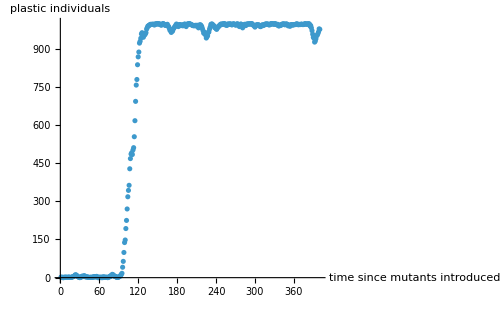

```mathematica
table1=Table[{i,Length[Flatten[Position[data[[i*1000+2;;( i)*1000+1000]][[All,4]],_?(#==-1&)]]]}, {i, 1, 400}];
ListPlot[table1, PlotRange->{All,All}, AxesLabel->{"time since mutants introduced","plastic individuals"}, ImageSize->500]
```

```mathematica
lowest=table1[[Flatten[Position[table1[[All,2]],Nearest[table1[[All,2]], lowval][[1]]]]]][[1]][[1]];
highest = table1[[Flatten[Position[table1[[All,2]],Nearest[table1[[All,2]], highval][[1]]]]]][[1]][[1]];
Print[lowest, " , ", highest]
```

100 , 119

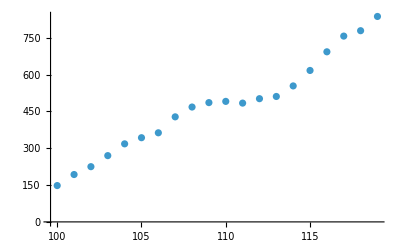

```mathematica
table1=Table[{i,Length[Flatten[Position[data[[i*1000+2;;( i)*1000+1000]][[All,4]],_?(#==-1&)]]]}, {i, lowest, highest}];
ListPlot[table1]
```

#### Bin the data (3)

```mathematica
sumallelements={};
For[tt = lowest,tt<=highest, tt++,
bottomtime=tt;
toptime=bottomtime+1;

allplastics=Flatten[Position[Drop[data,1][[All,4]][[bottomtime*1000+1;;toptime*1000]],-1]];

avgdists=Drop[data,1][[All,3]][[bottomtime*1000+1;;toptime*1000]][[allplastics]];
originalTP = Table[{Drop[data[[All,8+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allplastics]],Drop[data[[All,9+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allplastics]]}, {i, 0, 10}];
TP=Table[Transpose[originalTP[[i]]],{i, 1, 11}];
allcoordsbefore={};

For[i0 = 1, i0 <Length[TP[[1]]],i0++,
nonfloors=TP[[All,i0]][[All,1]];
partitions=BinCounts[nonfloors,{0,1001,1}];
dropempties=TakeList[nonfloors,partitions]/. {}->Nothing;
floor1=Map[Floor, Map[Mean,dropempties]];
deltaps=TakeList[TP[[All,i0]][[All,2]],partitions]/.{}-> Nothing;
deltap1=Map[Mean,deltaps];

floor1=floor1/. 0 -> 1;

inputnums=Table[0, {i, 1, 1001}];
inputnums[[1;;floor1[[1]]]] = deltap1[[1]];
For[i =1, i <Length[floor1],i++,
inputnums[[floor1[[i]];;floor1[[i+1]]]] = deltap1[[i+1]]
];
AppendTo[allcoordsbefore,Transpose[{Table[avgdists[[i0]],{k, 1, 1001}],Range[1,1001], inputnums}]];
];
densitylistbefore=allcoordsbefore;
densitylistbefore = Flatten[densitylistbefore,1];

maxdist = 50;
maxT = 50;
partitiongrid = 50;

list=Sort[densitylistbefore, #1[[1]]<#2[[1]]&];
partitions=BinCounts[list[[All,1]],maxdist/partitiongrid];
binnedcoords=TakeList[list,partitions];

binnedsublists = {};
For[i = 1, i ≤ Length[binnedcoords], i++,
list=Sort[binnedcoords[[i]], #1[[2]]<#2[[2]]&];
If[list ≠ {},
partitions=BinCounts[list[[All,2]],maxT/partitiongrid];
AppendTo[binnedsublists,TakeList[list,partitions]];
];
];

binnedsublistsbefore=binnedsublists;
totaldeltaP={};
mindeltaP={};
maxdeltaP={};
standarddevdeltaP={};

min=5;
max=50;
binnedsublists=binnedsublistsbefore;

For[i = 1, i <= Length[binnedsublists],i++,
For[j = 1, j<= Length[binnedsublists[[i]]],j++,
If[binnedsublists[[i]][[j]] != {},
If[Floor[binnedsublists[[i]][[j]][[1]][[1]]] <= max &&Floor[binnedsublists[[i]][[j]][[1]][[1]]] >= min,
AppendTo[totaldeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Total[binnedsublists[[i]][[j]][[All,3]]]}];
];
AppendTo[mindeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Min[binnedsublists[[i]][[j]][[All,3]]]}];
AppendTo[maxdeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Max[binnedsublists[[i]][[j]][[All,3]]]}];
]
]
];

totaldeltaPbefore=totaldeltaP;
standarddevdeltaPbefore=standarddevdeltaP;

maxbefore=Max[totaldeltaP[[All,3]]];
minbefore=Min[totaldeltaP[[All,3]]];

If[minbefore !=maxbefore,
mindensityb=minbefore;
maxdensityb=maxbefore;,
mindensityb = 0;
maxdensityb = 1;
];

If[maxdensityb==0,
maxdensityb=1;
d0b=-mindensityb/(maxdensityb-mindensityb),

];

d0b=-mindensityb/(maxdensityb-mindensityb);
piece1b[x_]:=d0b/(Log[-mindensityb+1])*Log[x-mindensityb+1];
piece2b[x_]:=((1-d0b)/(maxdensityb)^2)*x^2+d0b;
pwb[x_]:=Piecewise[{{piece1b[x], x < 0},{piece2b[x], x >=0} }];

delta=1;
deltad0=.003;

underlyingcolorbefore[z_]:=Map[Piecewise,{Join[Table[{redtowhite[i*(d0b-deltad0)/(18*(d0b-deltad0))],(i-1*delta)*d0b*.05<=z<i*d0b*.05},{i, 1, 18,delta}],{{RGBColor[1,.9,.9],18*d0b*.05<=z<d0b-deltad0*1.5},{RGBColor[1,.95,.95],d0b-deltad0*1.5<=z<d0b-deltad0},{RGBColor[1,1,1],(d0b-deltad0)<=z≤(d0b+deltad0)}},Table[{whitetoblue[(1-d0b-deltad0)*i/(18*(1-d0b-deltad0))],d0b+deltad0+(1-(d0b+deltad0))/18*(i-1)<z<=d0b+deltad0+(1-(d0b+deltad0))/18*(i)},{i, 1, 18,1}],{{RGBColor[0,0,1],1<z<100}}]}];

colordensityfunctionbefore[x_]:= underlyingcolorbefore[pwb[x]];
plotlegendbefore=BarLegend[{colordensityfunctionbefore,{mindensityb,maxdensityb}},LegendLabel->"Δ P", LabelStyle->Directive[Bold, Medium, Black,15]];

transformedcolorbefore=Table[underlyingcolorbefore[pwb[totaldeltaPbefore[[i]][[3]]]],{i, 1, Length[totaldeltaPbefore[[All,3]]]}];

AppendTo[sumallelements, totaldeltaPbefore];
]
```

```mathematica
sumallelements3plastic = sumallelements;
```

#### Import simulation 4

```mathematica
data = Import["threshold_payoff_ranges_4.txt","CSV"];
```

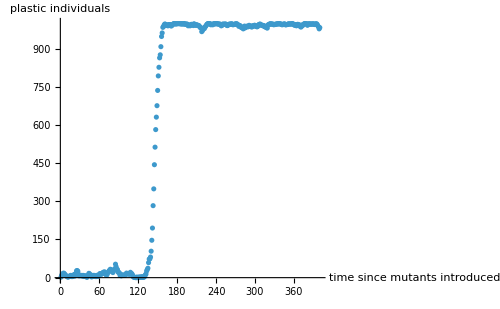

```mathematica
table1=Table[{i,Length[Flatten[Position[data[[i*1000+2;;( i)*1000+1000]][[All,4]],_?(#==-1&)]]]}, {i, 1, 400}];
ListPlot[table1, PlotRange->{All,All}, AxesLabel->{"time since mutants introduced","plastic individuals"}, ImageSize->500]
```

```mathematica
lowest=table1[[Flatten[Position[table1[[All,2]],Nearest[table1[[All,2]], lowval][[1]]]]]][[1]][[1]];
highest = table1[[Flatten[Position[table1[[All,2]],Nearest[table1[[All,2]], highval][[1]]]]]][[1]][[1]];
Print[lowest, " , ", highest]
```

141 , 153

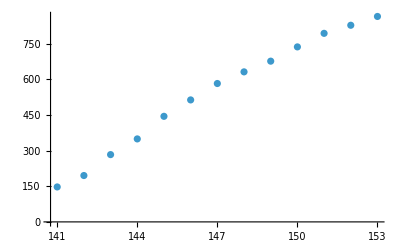

```mathematica
table1=Table[{i,Length[Flatten[Position[data[[i*1000+2;;( i)*1000+1000]][[All,4]],_?(#==-1&)]]]}, {i, lowest, highest}];
ListPlot[table1]
```

#### Bin the data (4)

```mathematica
sumallelements={};
For[tt = lowest,tt<=highest, tt++,
bottomtime=tt;
toptime=bottomtime+1;

allplastics=Flatten[Position[Drop[data,1][[All,4]][[bottomtime*1000+1;;toptime*1000]],-1]];

avgdists=Drop[data,1][[All,3]][[bottomtime*1000+1;;toptime*1000]][[allplastics]];
originalTP = Table[{Drop[data[[All,8+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allplastics]],Drop[data[[All,9+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allplastics]]}, {i, 0, 10}];
TP=Table[Transpose[originalTP[[i]]],{i, 1, 11}];
allcoordsbefore={};

For[i0 = 1, i0 <Length[TP[[1]]],i0++,
nonfloors=TP[[All,i0]][[All,1]];
partitions=BinCounts[nonfloors,{0,1001,1}];
dropempties=TakeList[nonfloors,partitions]/. {}->Nothing;
floor1=Map[Floor, Map[Mean,dropempties]];
deltaps=TakeList[TP[[All,i0]][[All,2]],partitions]/.{}-> Nothing;
deltap1=Map[Mean,deltaps];

floor1=floor1/. 0 -> 1;

inputnums=Table[0, {i, 1, 1001}];
inputnums[[1;;floor1[[1]]]] = deltap1[[1]];
For[i =1, i <Length[floor1],i++,
inputnums[[floor1[[i]];;floor1[[i+1]]]] = deltap1[[i+1]]
];
AppendTo[allcoordsbefore,Transpose[{Table[avgdists[[i0]],{k, 1, 1001}],Range[1,1001], inputnums}]];
];
densitylistbefore=allcoordsbefore;
densitylistbefore = Flatten[densitylistbefore,1];

maxdist = 50;
maxT = 50;
partitiongrid = 50;

list=Sort[densitylistbefore, #1[[1]]<#2[[1]]&];
partitions=BinCounts[list[[All,1]],maxdist/partitiongrid];
binnedcoords=TakeList[list,partitions];

binnedsublists = {};
For[i = 1, i ≤ Length[binnedcoords], i++,
list=Sort[binnedcoords[[i]], #1[[2]]<#2[[2]]&];
If[list ≠ {},
partitions=BinCounts[list[[All,2]],maxT/partitiongrid];
AppendTo[binnedsublists,TakeList[list,partitions]];
];
];

binnedsublistsbefore=binnedsublists;
totaldeltaP={};
mindeltaP={};
maxdeltaP={};
standarddevdeltaP={};

min=5;
max=50;
binnedsublists=binnedsublistsbefore;

For[i = 1, i <= Length[binnedsublists],i++,
For[j = 1, j<= Length[binnedsublists[[i]]],j++,
If[binnedsublists[[i]][[j]] != {},
If[Floor[binnedsublists[[i]][[j]][[1]][[1]]] <= max &&Floor[binnedsublists[[i]][[j]][[1]][[1]]] >= min,
AppendTo[totaldeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Total[binnedsublists[[i]][[j]][[All,3]]]}];
];
AppendTo[mindeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Min[binnedsublists[[i]][[j]][[All,3]]]}];
AppendTo[maxdeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Max[binnedsublists[[i]][[j]][[All,3]]]}];
]
]
];

totaldeltaPbefore=totaldeltaP;
standarddevdeltaPbefore=standarddevdeltaP;

maxbefore=Max[totaldeltaP[[All,3]]];
minbefore=Min[totaldeltaP[[All,3]]];

If[minbefore !=maxbefore,
mindensityb=minbefore;
maxdensityb=maxbefore;,
mindensityb = 0;
maxdensityb = 1;
];

If[maxdensityb==0,
maxdensityb=1;
d0b=-mindensityb/(maxdensityb-mindensityb),

];

d0b=-mindensityb/(maxdensityb-mindensityb);
piece1b[x_]:=d0b/(Log[-mindensityb+1])*Log[x-mindensityb+1];
piece2b[x_]:=((1-d0b)/(maxdensityb)^2)*x^2+d0b;
pwb[x_]:=Piecewise[{{piece1b[x], x < 0},{piece2b[x], x >=0} }];

delta=1;
deltad0=.003;

underlyingcolorbefore[z_]:=Map[Piecewise,{Join[Table[{redtowhite[i*(d0b-deltad0)/(18*(d0b-deltad0))],(i-1*delta)*d0b*.05<=z<i*d0b*.05},{i, 1, 18,delta}],{{RGBColor[1,.9,.9],18*d0b*.05<=z<d0b-deltad0*1.5},{RGBColor[1,.95,.95],d0b-deltad0*1.5<=z<d0b-deltad0},{RGBColor[1,1,1],(d0b-deltad0)<=z≤(d0b+deltad0)}},Table[{whitetoblue[(1-d0b-deltad0)*i/(18*(1-d0b-deltad0))],d0b+deltad0+(1-(d0b+deltad0))/18*(i-1)<z<=d0b+deltad0+(1-(d0b+deltad0))/18*(i)},{i, 1, 18,1}],{{RGBColor[0,0,1],1<z<100}}]}];

colordensityfunctionbefore[x_]:= underlyingcolorbefore[pwb[x]];
plotlegendbefore=BarLegend[{colordensityfunctionbefore,{mindensityb,maxdensityb}},LegendLabel->"Δ P", LabelStyle->Directive[Bold, Medium, Black,15]];

transformedcolorbefore=Table[underlyingcolorbefore[pwb[totaldeltaPbefore[[i]][[3]]]],{i, 1, Length[totaldeltaPbefore[[All,3]]]}];

AppendTo[sumallelements, totaldeltaPbefore];
]
```

```mathematica
sumallelements4plastic = sumallelements;
```

#### Import simulation 5

```mathematica
data = Import["threshold_payoff_ranges_5.txt","CSV"];
```

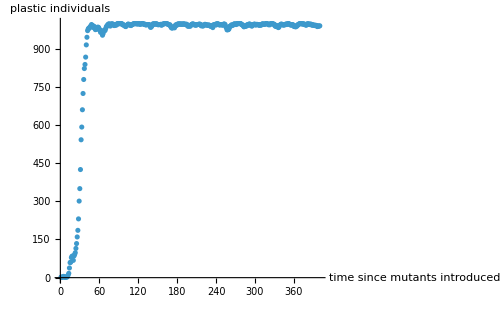

```mathematica
table1=Table[{i,Length[Flatten[Position[data[[i*1000+2;;( i)*1000+1000]][[All,4]],_?(#==-1&)]]]}, {i, 1, 400}];
ListPlot[table1, PlotRange->{All,All}, AxesLabel->{"time since mutants introduced","plastic individuals"}, ImageSize->500]
```

```mathematica
lowest=table1[[Flatten[Position[table1[[All,2]],Nearest[table1[[All,2]], lowval][[1]]]]]][[1]][[1]];
highest = table1[[Flatten[Position[table1[[All,2]],Nearest[table1[[All,2]], highval][[1]]]]]][[1]][[1]];
Print[lowest, " , ", highest]
```

26 , 38

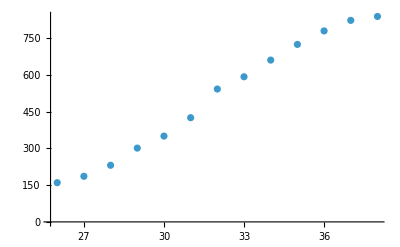

```mathematica
table1=Table[{i,Length[Flatten[Position[data[[i*1000+2;;( i)*1000+1000]][[All,4]],_?(#==-1&)]]]}, {i, lowest, highest}];
ListPlot[table1]
```

#### Bin the data (5)

```mathematica
sumallelements={};
For[tt = lowest,tt<=highest, tt++,
bottomtime=tt;
toptime=bottomtime+1;

allplastics=Flatten[Position[Drop[data,1][[All,4]][[bottomtime*1000+1;;toptime*1000]],-1]];

avgdists=Drop[data,1][[All,3]][[bottomtime*1000+1;;toptime*1000]][[allplastics]];
originalTP = Table[{Drop[data[[All,8+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allplastics]],Drop[data[[All,9+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allplastics]]}, {i, 0, 10}];
TP=Table[Transpose[originalTP[[i]]],{i, 1, 11}];
allcoordsbefore={};

For[i0 = 1, i0 <Length[TP[[1]]],i0++,
nonfloors=TP[[All,i0]][[All,1]];
partitions=BinCounts[nonfloors,{0,1001,1}];
dropempties=TakeList[nonfloors,partitions]/. {}->Nothing;
floor1=Map[Floor, Map[Mean,dropempties]];
deltaps=TakeList[TP[[All,i0]][[All,2]],partitions]/.{}-> Nothing;
deltap1=Map[Mean,deltaps];

floor1=floor1/. 0 -> 1;

inputnums=Table[0, {i, 1, 1001}];
inputnums[[1;;floor1[[1]]]] = deltap1[[1]];
For[i =1, i <Length[floor1],i++,
inputnums[[floor1[[i]];;floor1[[i+1]]]] = deltap1[[i+1]]
];
AppendTo[allcoordsbefore,Transpose[{Table[avgdists[[i0]],{k, 1, 1001}],Range[1,1001], inputnums}]];
];
densitylistbefore=allcoordsbefore;
densitylistbefore = Flatten[densitylistbefore,1];

maxdist = 50;
maxT = 50;
partitiongrid = 50;

list=Sort[densitylistbefore, #1[[1]]<#2[[1]]&];
partitions=BinCounts[list[[All,1]],maxdist/partitiongrid];
binnedcoords=TakeList[list,partitions];

binnedsublists = {};
For[i = 1, i ≤ Length[binnedcoords], i++,
list=Sort[binnedcoords[[i]], #1[[2]]<#2[[2]]&];
If[list ≠ {},
partitions=BinCounts[list[[All,2]],maxT/partitiongrid];
AppendTo[binnedsublists,TakeList[list,partitions]];
];
];

binnedsublistsbefore=binnedsublists;
totaldeltaP={};
mindeltaP={};
maxdeltaP={};
standarddevdeltaP={};

min=5;
max=50;
binnedsublists=binnedsublistsbefore;

For[i = 1, i <= Length[binnedsublists],i++,
For[j = 1, j<= Length[binnedsublists[[i]]],j++,
If[binnedsublists[[i]][[j]] != {},
If[Floor[binnedsublists[[i]][[j]][[1]][[1]]] <= max &&Floor[binnedsublists[[i]][[j]][[1]][[1]]] >= min,
AppendTo[totaldeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Total[binnedsublists[[i]][[j]][[All,3]]]}];
];
AppendTo[mindeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Min[binnedsublists[[i]][[j]][[All,3]]]}];
AppendTo[maxdeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Max[binnedsublists[[i]][[j]][[All,3]]]}];
]
]
];

totaldeltaPbefore=totaldeltaP;
standarddevdeltaPbefore=standarddevdeltaP;

maxbefore=Max[totaldeltaP[[All,3]]];
minbefore=Min[totaldeltaP[[All,3]]];

If[minbefore !=maxbefore,
mindensityb=minbefore;
maxdensityb=maxbefore;,
mindensityb = 0;
maxdensityb = 1;
];

If[maxdensityb==0,
maxdensityb=1;
d0b=-mindensityb/(maxdensityb-mindensityb),

];

d0b=-mindensityb/(maxdensityb-mindensityb);
piece1b[x_]:=d0b/(Log[-mindensityb+1])*Log[x-mindensityb+1];
piece2b[x_]:=((1-d0b)/(maxdensityb)^2)*x^2+d0b;
pwb[x_]:=Piecewise[{{piece1b[x], x < 0},{piece2b[x], x >=0} }];

delta=1;
deltad0=.003;

underlyingcolorbefore[z_]:=Map[Piecewise,{Join[Table[{redtowhite[i*(d0b-deltad0)/(18*(d0b-deltad0))],(i-1*delta)*d0b*.05<=z<i*d0b*.05},{i, 1, 18,delta}],{{RGBColor[1,.9,.9],18*d0b*.05<=z<d0b-deltad0*1.5},{RGBColor[1,.95,.95],d0b-deltad0*1.5<=z<d0b-deltad0},{RGBColor[1,1,1],(d0b-deltad0)<=z≤(d0b+deltad0)}},Table[{whitetoblue[(1-d0b-deltad0)*i/(18*(1-d0b-deltad0))],d0b+deltad0+(1-(d0b+deltad0))/18*(i-1)<z<=d0b+deltad0+(1-(d0b+deltad0))/18*(i)},{i, 1, 18,1}],{{RGBColor[0,0,1],1<z<100}}]}];

colordensityfunctionbefore[x_]:= underlyingcolorbefore[pwb[x]];
plotlegendbefore=BarLegend[{colordensityfunctionbefore,{mindensityb,maxdensityb}},LegendLabel->"Δ P", LabelStyle->Directive[Bold, Medium, Black,15]];

transformedcolorbefore=Table[underlyingcolorbefore[pwb[totaldeltaPbefore[[i]][[3]]]],{i, 1, Length[totaldeltaPbefore[[All,3]]]}];

AppendTo[sumallelements, totaldeltaPbefore];
]
```

```mathematica
sumallelements5plastic = sumallelements;
```

### Compile plastic data :

```mathematica
sumallelements = Join[sumallelements1plastic,sumallelements2plastic, sumallelements3plastic,sumallelements4plastic,sumallelements5plastic]
```

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data"];
Export["fig3_all_runs_plastic_fitnesses.txt", Flatten[sumallelements]];
SetDirectory[currentdir];
```

### For innate individuals:

#### Import simulation 1

```mathematica
data = Import["threshold_payoff_ranges_1.txt","CSV"];
```

```mathematica
table1=Table[{i,Length[Flatten[Position[data[[i*1000+2;;( i)*1000+1000]][[All,4]],_?(#==-1&)]]]}, {i, 1, 400}];
ListPlot[table1, PlotRange->{All,All}, AxesLabel->{"time since mutants introduced","plastic individuals"}, ImageSize->500]
```

-Graphics-

```mathematica
lowest=table1[[Flatten[Position[table1[[All,2]],Nearest[table1[[All,2]], lowval][[1]]]]]][[1]][[1]];
highest = table1[[Flatten[Position[table1[[All,2]],Nearest[table1[[All,2]], highval][[1]]]]]][[1]][[1]];
Print[lowest, " , ", highest]
```

20 , 31

```mathematica
table1=Table[{i,Length[Flatten[Position[data[[i*1000+2;;( i)*1000+1000]][[All,4]],_?(#==-1&)]]]}, {i, lowest, highest}];
ListPlot[table1]
```

-Graphics-

#### Bin the data (1)

```mathematica
sumallelements={};
For[tt = lowest,tt<=highest, tt++,
bottomtime=tt;
toptime=bottomtime+1;

allinnates=Flatten[Position[Drop[data,1][[All,4]][[bottomtime*1000+1;;toptime*1000]],1]];

avgdists=Drop[data,1][[All,3]][[bottomtime*1000+1;;toptime*1000]][[allinnates]];
originalTP = Table[{Drop[data[[All,8+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allinnates]],Drop[data[[All,9+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allinnates]]}, {i, 0, 10}];
TP=Table[Transpose[originalTP[[i]]],{i, 1, 11}];
allcoordsbefore={};

For[i0 = 1, i0 <Length[TP[[1]]],i0++,
nonfloors=TP[[All,i0]][[All,1]];
partitions=BinCounts[nonfloors,{0,1001,1}];
dropempties=TakeList[nonfloors,partitions]/. {}->Nothing;
floor1=Map[Floor, Map[Mean,dropempties]];
deltaps=TakeList[TP[[All,i0]][[All,2]],partitions]/.{}-> Nothing;
deltap1=Map[Mean,deltaps];

floor1=floor1/. 0 -> 1;

inputnums=Table[0, {i, 1, 1001}];
inputnums[[1;;floor1[[1]]]] = deltap1[[1]];
For[i =1, i <Length[floor1],i++,
inputnums[[floor1[[i]];;floor1[[i+1]]]] = deltap1[[i+1]]
];
AppendTo[allcoordsbefore,Transpose[{Table[avgdists[[i0]],{k, 1, 1001}],Range[1,1001], inputnums}]];
];
densitylistbefore=allcoordsbefore;
densitylistbefore = Flatten[densitylistbefore,1];

maxdist = 50;
maxT = 50;
partitiongrid = 50;

list=Sort[densitylistbefore, #1[[1]]<#2[[1]]&];
partitions=BinCounts[list[[All,1]],maxdist/partitiongrid];
binnedcoords=TakeList[list,partitions];

binnedsublists = {};
For[i = 1, i ≤ Length[binnedcoords], i++,
list=Sort[binnedcoords[[i]], #1[[2]]<#2[[2]]&];
If[list ≠ {},
partitions=BinCounts[list[[All,2]],maxT/partitiongrid];
AppendTo[binnedsublists,TakeList[list,partitions]];
];
];

binnedsublistsbefore=binnedsublists;
totaldeltaP={};
mindeltaP={};
maxdeltaP={};
standarddevdeltaP={};

min=5;
max=50;
binnedsublists=binnedsublistsbefore;

For[i = 1, i <= Length[binnedsublists],i++,
For[j = 1, j<= Length[binnedsublists[[i]]],j++,
If[binnedsublists[[i]][[j]] != {},
If[Floor[binnedsublists[[i]][[j]][[1]][[1]]] <= max &&Floor[binnedsublists[[i]][[j]][[1]][[1]]] >= min,
AppendTo[totaldeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Total[binnedsublists[[i]][[j]][[All,3]]]}];
];
AppendTo[mindeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Min[binnedsublists[[i]][[j]][[All,3]]]}];
AppendTo[maxdeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Max[binnedsublists[[i]][[j]][[All,3]]]}];
]
]
];

totaldeltaPbefore=totaldeltaP;
standarddevdeltaPbefore=standarddevdeltaP;

maxbefore=Max[totaldeltaP[[All,3]]];
minbefore=Min[totaldeltaP[[All,3]]];

If[minbefore !=maxbefore,
mindensityb=minbefore;
maxdensityb=maxbefore;,
mindensityb = 0;
maxdensityb = 1;
];

If[maxdensityb==0,
maxdensityb=1;
d0b=-mindensityb/(maxdensityb-mindensityb),

];

d0b=-mindensityb/(maxdensityb-mindensityb);
piece1b[x_]:=d0b/(Log[-mindensityb+1])*Log[x-mindensityb+1];
piece2b[x_]:=((1-d0b)/(maxdensityb)^2)*x^2+d0b;
pwb[x_]:=Piecewise[{{piece1b[x], x < 0},{piece2b[x], x >=0} }];

delta=1;
deltad0=.003;

underlyingcolorbefore[z_]:=Map[Piecewise,{Join[Table[{redtowhite[i*(d0b-deltad0)/(18*(d0b-deltad0))],(i-1*delta)*d0b*.05<=z<i*d0b*.05},{i, 1, 18,delta}],{{RGBColor[1,.9,.9],18*d0b*.05<=z<d0b-deltad0*1.5},{RGBColor[1,.95,.95],d0b-deltad0*1.5<=z<d0b-deltad0},{RGBColor[1,1,1],(d0b-deltad0)<=z≤(d0b+deltad0)}},Table[{whitetoblue[(1-d0b-deltad0)*i/(18*(1-d0b-deltad0))],d0b+deltad0+(1-(d0b+deltad0))/18*(i-1)<z<=d0b+deltad0+(1-(d0b+deltad0))/18*(i)},{i, 1, 18,1}],{{RGBColor[0,0,1],1<z<100}}]}];

colordensityfunctionbefore[x_]:= underlyingcolorbefore[pwb[x]];
plotlegendbefore=BarLegend[{colordensityfunctionbefore,{mindensityb,maxdensityb}},LegendLabel->"Δ P", LabelStyle->Directive[Bold, Medium, Black,15]];

transformedcolorbefore=Table[underlyingcolorbefore[pwb[totaldeltaPbefore[[i]][[3]]]],{i, 1, Length[totaldeltaPbefore[[All,3]]]}];

AppendTo[sumallelements, totaldeltaPbefore];
]
```

```mathematica
sumallelements1innates = sumallelements;
```

#### Import simulation 2

```mathematica
data = Import["threshold_payoff_ranges_2.txt","CSV"];
```

```mathematica
table1=Table[{i,Length[Flatten[Position[data[[i*1000+2;;( i)*1000+1000]][[All,4]],_?(#==-1&)]]]}, {i, 1, 400}];
ListPlot[table1, PlotRange->{All,All}, AxesLabel->{"time since mutants introduced","plastic individuals"}, ImageSize->500]
```

-Graphics-

```mathematica
lowest=table1[[Flatten[Position[table1[[All,2]],Nearest[table1[[All,2]], lowval][[1]]]]]][[1]][[1]];
highest = table1[[Flatten[Position[table1[[All,2]],Nearest[table1[[All,2]], highval][[1]]]]]][[1]][[1]];
Print[lowest, " , ", highest]
```

166 , 179

```mathematica
table1=Table[{i,Length[Flatten[Position[data[[i*1000+2;;( i)*1000+1000]][[All,4]],_?(#==-1&)]]]}, {i, lowest, highest}];
ListPlot[table1]
```

-Graphics-

#### Bin the data (2)

```mathematica
sumallelements={};
For[tt = lowest,tt<=highest, tt++,
bottomtime=tt;
toptime=bottomtime+1;

allinnates=Flatten[Position[Drop[data,1][[All,4]][[bottomtime*1000+1;;toptime*1000]],1]];

avgdists=Drop[data,1][[All,3]][[bottomtime*1000+1;;toptime*1000]][[allinnates]];
originalTP = Table[{Drop[data[[All,8+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allinnates]],Drop[data[[All,9+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allinnates]]}, {i, 0, 10}];
TP=Table[Transpose[originalTP[[i]]],{i, 1, 11}];
allcoordsbefore={};

For[i0 = 1, i0 <Length[TP[[1]]],i0++,
nonfloors=TP[[All,i0]][[All,1]];
partitions=BinCounts[nonfloors,{0,1001,1}];
dropempties=TakeList[nonfloors,partitions]/. {}->Nothing;
floor1=Map[Floor, Map[Mean,dropempties]];
deltaps=TakeList[TP[[All,i0]][[All,2]],partitions]/.{}-> Nothing;
deltap1=Map[Mean,deltaps];

floor1=floor1/. 0 -> 1;

inputnums=Table[0, {i, 1, 1001}];
inputnums[[1;;floor1[[1]]]] = deltap1[[1]];
For[i =1, i <Length[floor1],i++,
inputnums[[floor1[[i]];;floor1[[i+1]]]] = deltap1[[i+1]]
];
AppendTo[allcoordsbefore,Transpose[{Table[avgdists[[i0]],{k, 1, 1001}],Range[1,1001], inputnums}]];
];
densitylistbefore=allcoordsbefore;
densitylistbefore = Flatten[densitylistbefore,1];

maxdist = 50;
maxT = 50;
partitiongrid = 50;

list=Sort[densitylistbefore, #1[[1]]<#2[[1]]&];
partitions=BinCounts[list[[All,1]],maxdist/partitiongrid];
binnedcoords=TakeList[list,partitions];

binnedsublists = {};
For[i = 1, i ≤ Length[binnedcoords], i++,
list=Sort[binnedcoords[[i]], #1[[2]]<#2[[2]]&];
If[list ≠ {},
partitions=BinCounts[list[[All,2]],maxT/partitiongrid];
AppendTo[binnedsublists,TakeList[list,partitions]];
];
];

binnedsublistsbefore=binnedsublists;
totaldeltaP={};
mindeltaP={};
maxdeltaP={};
standarddevdeltaP={};

min=5;
max=50;
binnedsublists=binnedsublistsbefore;

For[i = 1, i <= Length[binnedsublists],i++,
For[j = 1, j<= Length[binnedsublists[[i]]],j++,
If[binnedsublists[[i]][[j]] != {},
If[Floor[binnedsublists[[i]][[j]][[1]][[1]]] <= max &&Floor[binnedsublists[[i]][[j]][[1]][[1]]] >= min,
AppendTo[totaldeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Total[binnedsublists[[i]][[j]][[All,3]]]}];
];
AppendTo[mindeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Min[binnedsublists[[i]][[j]][[All,3]]]}];
AppendTo[maxdeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Max[binnedsublists[[i]][[j]][[All,3]]]}];
]
]
];

totaldeltaPbefore=totaldeltaP;
standarddevdeltaPbefore=standarddevdeltaP;

maxbefore=Max[totaldeltaP[[All,3]]];
minbefore=Min[totaldeltaP[[All,3]]];

If[minbefore !=maxbefore,
mindensityb=minbefore;
maxdensityb=maxbefore;,
mindensityb = 0;
maxdensityb = 1;
];

If[maxdensityb==0,
maxdensityb=1;
d0b=-mindensityb/(maxdensityb-mindensityb),

];

d0b=-mindensityb/(maxdensityb-mindensityb);
piece1b[x_]:=d0b/(Log[-mindensityb+1])*Log[x-mindensityb+1];
piece2b[x_]:=((1-d0b)/(maxdensityb)^2)*x^2+d0b;
pwb[x_]:=Piecewise[{{piece1b[x], x < 0},{piece2b[x], x >=0} }];

delta=1;
deltad0=.003;

underlyingcolorbefore[z_]:=Map[Piecewise,{Join[Table[{redtowhite[i*(d0b-deltad0)/(18*(d0b-deltad0))],(i-1*delta)*d0b*.05<=z<i*d0b*.05},{i, 1, 18,delta}],{{RGBColor[1,.9,.9],18*d0b*.05<=z<d0b-deltad0*1.5},{RGBColor[1,.95,.95],d0b-deltad0*1.5<=z<d0b-deltad0},{RGBColor[1,1,1],(d0b-deltad0)<=z≤(d0b+deltad0)}},Table[{whitetoblue[(1-d0b-deltad0)*i/(18*(1-d0b-deltad0))],d0b+deltad0+(1-(d0b+deltad0))/18*(i-1)<z<=d0b+deltad0+(1-(d0b+deltad0))/18*(i)},{i, 1, 18,1}],{{RGBColor[0,0,1],1<z<100}}]}];

colordensityfunctionbefore[x_]:= underlyingcolorbefore[pwb[x]];
plotlegendbefore=BarLegend[{colordensityfunctionbefore,{mindensityb,maxdensityb}},LegendLabel->"Δ P", LabelStyle->Directive[Bold, Medium, Black,15]];

transformedcolorbefore=Table[underlyingcolorbefore[pwb[totaldeltaPbefore[[i]][[3]]]],{i, 1, Length[totaldeltaPbefore[[All,3]]]}];

AppendTo[sumallelements, totaldeltaPbefore];
]
```

```mathematica
sumallelements2innates = sumallelements;
```

#### Import simulation 3

```mathematica
data = Import["threshold_payoff_ranges_3.txt","CSV"];
```

```mathematica
table1=Table[{i,Length[Flatten[Position[data[[i*1000+2;;( i)*1000+1000]][[All,4]],_?(#==-1&)]]]}, {i, 1, 400}];
ListPlot[table1, PlotRange->{All,All}, AxesLabel->{"time since mutants introduced","plastic individuals"}, ImageSize->500]
```

-Graphics-

```mathematica
lowest=table1[[Flatten[Position[table1[[All,2]],Nearest[table1[[All,2]], lowval][[1]]]]]][[1]][[1]];
highest = table1[[Flatten[Position[table1[[All,2]],Nearest[table1[[All,2]], highval][[1]]]]]][[1]][[1]];
Print[lowest, " , ", highest]
```

100 , 119

```mathematica
table1=Table[{i,Length[Flatten[Position[data[[i*1000+2;;( i)*1000+1000]][[All,4]],_?(#==-1&)]]]}, {i, lowest, highest}];
ListPlot[table1]
```

-Graphics-

#### Bin the data (3)

```mathematica
sumallelements={};
For[tt = lowest,tt<=highest, tt++,
bottomtime=tt;
toptime=bottomtime+1;

allinnates=Flatten[Position[Drop[data,1][[All,4]][[bottomtime*1000+1;;toptime*1000]],1]];

avgdists=Drop[data,1][[All,3]][[bottomtime*1000+1;;toptime*1000]][[allinnates]];
originalTP = Table[{Drop[data[[All,8+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allinnates]],Drop[data[[All,9+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allinnates]]}, {i, 0, 10}];
TP=Table[Transpose[originalTP[[i]]],{i, 1, 11}];
allcoordsbefore={};

For[i0 = 1, i0 <Length[TP[[1]]],i0++,
nonfloors=TP[[All,i0]][[All,1]];
partitions=BinCounts[nonfloors,{0,1001,1}];
dropempties=TakeList[nonfloors,partitions]/. {}->Nothing;
floor1=Map[Floor, Map[Mean,dropempties]];
deltaps=TakeList[TP[[All,i0]][[All,2]],partitions]/.{}-> Nothing;
deltap1=Map[Mean,deltaps];

floor1=floor1/. 0 -> 1;

inputnums=Table[0, {i, 1, 1001}];
inputnums[[1;;floor1[[1]]]] = deltap1[[1]];
For[i =1, i <Length[floor1],i++,
inputnums[[floor1[[i]];;floor1[[i+1]]]] = deltap1[[i+1]]
];
AppendTo[allcoordsbefore,Transpose[{Table[avgdists[[i0]],{k, 1, 1001}],Range[1,1001], inputnums}]];
];
densitylistbefore=allcoordsbefore;
densitylistbefore = Flatten[densitylistbefore,1];

maxdist = 50;
maxT = 50;
partitiongrid = 50;

list=Sort[densitylistbefore, #1[[1]]<#2[[1]]&];
partitions=BinCounts[list[[All,1]],maxdist/partitiongrid];
binnedcoords=TakeList[list,partitions];

binnedsublists = {};
For[i = 1, i ≤ Length[binnedcoords], i++,
list=Sort[binnedcoords[[i]], #1[[2]]<#2[[2]]&];
If[list ≠ {},
partitions=BinCounts[list[[All,2]],maxT/partitiongrid];
AppendTo[binnedsublists,TakeList[list,partitions]];
];
];

binnedsublistsbefore=binnedsublists;
totaldeltaP={};
mindeltaP={};
maxdeltaP={};
standarddevdeltaP={};

min=5;
max=50;
binnedsublists=binnedsublistsbefore;

For[i = 1, i <= Length[binnedsublists],i++,
For[j = 1, j<= Length[binnedsublists[[i]]],j++,
If[binnedsublists[[i]][[j]] != {},
If[Floor[binnedsublists[[i]][[j]][[1]][[1]]] <= max &&Floor[binnedsublists[[i]][[j]][[1]][[1]]] >= min,
AppendTo[totaldeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Total[binnedsublists[[i]][[j]][[All,3]]]}];
];
AppendTo[mindeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Min[binnedsublists[[i]][[j]][[All,3]]]}];
AppendTo[maxdeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Max[binnedsublists[[i]][[j]][[All,3]]]}];
]
]
];

totaldeltaPbefore=totaldeltaP;
standarddevdeltaPbefore=standarddevdeltaP;

maxbefore=Max[totaldeltaP[[All,3]]];
minbefore=Min[totaldeltaP[[All,3]]];

If[minbefore !=maxbefore,
mindensityb=minbefore;
maxdensityb=maxbefore;,
mindensityb = 0;
maxdensityb = 1;
];

If[maxdensityb==0,
maxdensityb=1;
d0b=-mindensityb/(maxdensityb-mindensityb),

];

d0b=-mindensityb/(maxdensityb-mindensityb);
piece1b[x_]:=d0b/(Log[-mindensityb+1])*Log[x-mindensityb+1];
piece2b[x_]:=((1-d0b)/(maxdensityb)^2)*x^2+d0b;
pwb[x_]:=Piecewise[{{piece1b[x], x < 0},{piece2b[x], x >=0} }];

delta=1;
deltad0=.003;

underlyingcolorbefore[z_]:=Map[Piecewise,{Join[Table[{redtowhite[i*(d0b-deltad0)/(18*(d0b-deltad0))],(i-1*delta)*d0b*.05<=z<i*d0b*.05},{i, 1, 18,delta}],{{RGBColor[1,.9,.9],18*d0b*.05<=z<d0b-deltad0*1.5},{RGBColor[1,.95,.95],d0b-deltad0*1.5<=z<d0b-deltad0},{RGBColor[1,1,1],(d0b-deltad0)<=z≤(d0b+deltad0)}},Table[{whitetoblue[(1-d0b-deltad0)*i/(18*(1-d0b-deltad0))],d0b+deltad0+(1-(d0b+deltad0))/18*(i-1)<z<=d0b+deltad0+(1-(d0b+deltad0))/18*(i)},{i, 1, 18,1}],{{RGBColor[0,0,1],1<z<100}}]}];

colordensityfunctionbefore[x_]:= underlyingcolorbefore[pwb[x]];
plotlegendbefore=BarLegend[{colordensityfunctionbefore,{mindensityb,maxdensityb}},LegendLabel->"Δ P", LabelStyle->Directive[Bold, Medium, Black,15]];

transformedcolorbefore=Table[underlyingcolorbefore[pwb[totaldeltaPbefore[[i]][[3]]]],{i, 1, Length[totaldeltaPbefore[[All,3]]]}];

AppendTo[sumallelements, totaldeltaPbefore];
]
```

```mathematica
sumallelements3innates = sumallelements;
```

#### Import simulation 4

```mathematica
data = Import["threshold_payoff_ranges_4.txt","CSV"];
```

```mathematica
table1=Table[{i,Length[Flatten[Position[data[[i*1000+2;;( i)*1000+1000]][[All,4]],_?(#==-1&)]]]}, {i, 1, 400}];
ListPlot[table1, PlotRange->{All,All}, AxesLabel->{"time since mutants introduced","plastic individuals"}, ImageSize->500]
```

-Graphics-

```mathematica
lowest=table1[[Flatten[Position[table1[[All,2]],Nearest[table1[[All,2]], lowval][[1]]]]]][[1]][[1]];
highest = table1[[Flatten[Position[table1[[All,2]],Nearest[table1[[All,2]], highval][[1]]]]]][[1]][[1]];
Print[lowest, " , ", highest]
```

141 , 153

```mathematica
table1=Table[{i,Length[Flatten[Position[data[[i*1000+2;;( i)*1000+1000]][[All,4]],_?(#==-1&)]]]}, {i, lowest, highest}];
ListPlot[table1]
```

-Graphics-

#### Bin the data (4)

```mathematica
sumallelements={};
For[tt = lowest,tt<=highest, tt++,
bottomtime=tt;
toptime=bottomtime+1;

allinnates=Flatten[Position[Drop[data,1][[All,4]][[bottomtime*1000+1;;toptime*1000]],1]];

avgdists=Drop[data,1][[All,3]][[bottomtime*1000+1;;toptime*1000]][[allinnates]];
originalTP = Table[{Drop[data[[All,8+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allinnates]],Drop[data[[All,9+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allinnates]]}, {i, 0, 10}];
TP=Table[Transpose[originalTP[[i]]],{i, 1, 11}];
allcoordsbefore={};

For[i0 = 1, i0 <Length[TP[[1]]],i0++,
nonfloors=TP[[All,i0]][[All,1]];
partitions=BinCounts[nonfloors,{0,1001,1}];
dropempties=TakeList[nonfloors,partitions]/. {}->Nothing;
floor1=Map[Floor, Map[Mean,dropempties]];
deltaps=TakeList[TP[[All,i0]][[All,2]],partitions]/.{}-> Nothing;
deltap1=Map[Mean,deltaps];

floor1=floor1/. 0 -> 1;

inputnums=Table[0, {i, 1, 1001}];
inputnums[[1;;floor1[[1]]]] = deltap1[[1]];
For[i =1, i <Length[floor1],i++,
inputnums[[floor1[[i]];;floor1[[i+1]]]] = deltap1[[i+1]]
];
AppendTo[allcoordsbefore,Transpose[{Table[avgdists[[i0]],{k, 1, 1001}],Range[1,1001], inputnums}]];
];
densitylistbefore=allcoordsbefore;
densitylistbefore = Flatten[densitylistbefore,1];

maxdist = 50;
maxT = 50;
partitiongrid = 50;

list=Sort[densitylistbefore, #1[[1]]<#2[[1]]&];
partitions=BinCounts[list[[All,1]],maxdist/partitiongrid];
binnedcoords=TakeList[list,partitions];

binnedsublists = {};
For[i = 1, i ≤ Length[binnedcoords], i++,
list=Sort[binnedcoords[[i]], #1[[2]]<#2[[2]]&];
If[list ≠ {},
partitions=BinCounts[list[[All,2]],maxT/partitiongrid];
AppendTo[binnedsublists,TakeList[list,partitions]];
];
];

binnedsublistsbefore=binnedsublists;
totaldeltaP={};
mindeltaP={};
maxdeltaP={};
standarddevdeltaP={};

min=5;
max=50;
binnedsublists=binnedsublistsbefore;

For[i = 1, i <= Length[binnedsublists],i++,
For[j = 1, j<= Length[binnedsublists[[i]]],j++,
If[binnedsublists[[i]][[j]] != {},
If[Floor[binnedsublists[[i]][[j]][[1]][[1]]] <= max &&Floor[binnedsublists[[i]][[j]][[1]][[1]]] >= min,
AppendTo[totaldeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Total[binnedsublists[[i]][[j]][[All,3]]]}];
];
AppendTo[mindeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Min[binnedsublists[[i]][[j]][[All,3]]]}];
AppendTo[maxdeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Max[binnedsublists[[i]][[j]][[All,3]]]}];
]
]
];

totaldeltaPbefore=totaldeltaP;
standarddevdeltaPbefore=standarddevdeltaP;

maxbefore=Max[totaldeltaP[[All,3]]];
minbefore=Min[totaldeltaP[[All,3]]];

If[minbefore !=maxbefore,
mindensityb=minbefore;
maxdensityb=maxbefore;,
mindensityb = 0;
maxdensityb = 1;
];

If[maxdensityb==0,
maxdensityb=1;
d0b=-mindensityb/(maxdensityb-mindensityb),

];

d0b=-mindensityb/(maxdensityb-mindensityb);
piece1b[x_]:=d0b/(Log[-mindensityb+1])*Log[x-mindensityb+1];
piece2b[x_]:=((1-d0b)/(maxdensityb)^2)*x^2+d0b;
pwb[x_]:=Piecewise[{{piece1b[x], x < 0},{piece2b[x], x >=0} }];

delta=1;
deltad0=.003;

underlyingcolorbefore[z_]:=Map[Piecewise,{Join[Table[{redtowhite[i*(d0b-deltad0)/(18*(d0b-deltad0))],(i-1*delta)*d0b*.05<=z<i*d0b*.05},{i, 1, 18,delta}],{{RGBColor[1,.9,.9],18*d0b*.05<=z<d0b-deltad0*1.5},{RGBColor[1,.95,.95],d0b-deltad0*1.5<=z<d0b-deltad0},{RGBColor[1,1,1],(d0b-deltad0)<=z≤(d0b+deltad0)}},Table[{whitetoblue[(1-d0b-deltad0)*i/(18*(1-d0b-deltad0))],d0b+deltad0+(1-(d0b+deltad0))/18*(i-1)<z<=d0b+deltad0+(1-(d0b+deltad0))/18*(i)},{i, 1, 18,1}],{{RGBColor[0,0,1],1<z<100}}]}];

colordensityfunctionbefore[x_]:= underlyingcolorbefore[pwb[x]];
plotlegendbefore=BarLegend[{colordensityfunctionbefore,{mindensityb,maxdensityb}},LegendLabel->"Δ P", LabelStyle->Directive[Bold, Medium, Black,15]];

transformedcolorbefore=Table[underlyingcolorbefore[pwb[totaldeltaPbefore[[i]][[3]]]],{i, 1, Length[totaldeltaPbefore[[All,3]]]}];

AppendTo[sumallelements, totaldeltaPbefore];
]
```

```mathematica
sumallelements4innates = sumallelements;
```

#### Import simulation 5

```mathematica
data = Import["threshold_payoff_ranges_5.txt","CSV"];
```

```mathematica
table1=Table[{i,Length[Flatten[Position[data[[i*1000+2;;( i)*1000+1000]][[All,4]],_?(#==-1&)]]]}, {i, 1, 400}];
ListPlot[table1, PlotRange->{All,All}, AxesLabel->{"time since mutants introduced","plastic individuals"}, ImageSize->500]
```

-Graphics-

```mathematica
lowest=table1[[Flatten[Position[table1[[All,2]],Nearest[table1[[All,2]], lowval][[1]]]]]][[1]][[1]];
highest = table1[[Flatten[Position[table1[[All,2]],Nearest[table1[[All,2]], highval][[1]]]]]][[1]][[1]];
Print[lowest, " , ", highest]
```

26 , 38

```mathematica
table1=Table[{i,Length[Flatten[Position[data[[i*1000+2;;( i)*1000+1000]][[All,4]],_?(#==-1&)]]]}, {i, lowest, highest}];
ListPlot[table1]
```

-Graphics-

#### Bin the data (5)

```mathematica
sumallelements={};
For[tt = lowest,tt<=highest, tt++,
bottomtime=tt;
toptime=bottomtime+1;

allinnates=Flatten[Position[Drop[data,1][[All,4]][[bottomtime*1000+1;;toptime*1000]],1]];

avgdists=Drop[data,1][[All,3]][[bottomtime*1000+1;;toptime*1000]][[allinnates]];
originalTP = Table[{Drop[data[[All,8+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allinnates]],Drop[data[[All,9+i*3]],1][[bottomtime*1000+1;;toptime*1000]][[allinnates]]}, {i, 0, 10}];
TP=Table[Transpose[originalTP[[i]]],{i, 1, 11}];
allcoordsbefore={};

For[i0 = 1, i0 <Length[TP[[1]]],i0++,
nonfloors=TP[[All,i0]][[All,1]];
partitions=BinCounts[nonfloors,{0,1001,1}];
dropempties=TakeList[nonfloors,partitions]/. {}->Nothing;
floor1=Map[Floor, Map[Mean,dropempties]];
deltaps=TakeList[TP[[All,i0]][[All,2]],partitions]/.{}-> Nothing;
deltap1=Map[Mean,deltaps];

floor1=floor1/. 0 -> 1;

inputnums=Table[0, {i, 1, 1001}];
inputnums[[1;;floor1[[1]]]] = deltap1[[1]];
For[i =1, i <Length[floor1],i++,
inputnums[[floor1[[i]];;floor1[[i+1]]]] = deltap1[[i+1]]
];
AppendTo[allcoordsbefore,Transpose[{Table[avgdists[[i0]],{k, 1, 1001}],Range[1,1001], inputnums}]];
];
densitylistbefore=allcoordsbefore;
densitylistbefore = Flatten[densitylistbefore,1];

maxdist = 50;
maxT = 50;
partitiongrid = 50;

list=Sort[densitylistbefore, #1[[1]]<#2[[1]]&];
partitions=BinCounts[list[[All,1]],maxdist/partitiongrid];
binnedcoords=TakeList[list,partitions];

binnedsublists = {};
For[i = 1, i ≤ Length[binnedcoords], i++,
list=Sort[binnedcoords[[i]], #1[[2]]<#2[[2]]&];
If[list ≠ {},
partitions=BinCounts[list[[All,2]],maxT/partitiongrid];
AppendTo[binnedsublists,TakeList[list,partitions]];
];
];

binnedsublistsbefore=binnedsublists;
totaldeltaP={};
mindeltaP={};
maxdeltaP={};
standarddevdeltaP={};

min=5;
max=50;
binnedsublists=binnedsublistsbefore;

For[i = 1, i <= Length[binnedsublists],i++,
For[j = 1, j<= Length[binnedsublists[[i]]],j++,
If[binnedsublists[[i]][[j]] != {},
If[Floor[binnedsublists[[i]][[j]][[1]][[1]]] <= max &&Floor[binnedsublists[[i]][[j]][[1]][[1]]] >= min,
AppendTo[totaldeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Total[binnedsublists[[i]][[j]][[All,3]]]}];
];
AppendTo[mindeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Min[binnedsublists[[i]][[j]][[All,3]]]}];
AppendTo[maxdeltaP, {Floor[binnedsublists[[i]][[j]][[1]][[1]]],Floor[binnedsublists[[i]][[j]][[1]][[2]]],Max[binnedsublists[[i]][[j]][[All,3]]]}];
]
]
];

totaldeltaPbefore=totaldeltaP;
standarddevdeltaPbefore=standarddevdeltaP;

maxbefore=Max[totaldeltaP[[All,3]]];
minbefore=Min[totaldeltaP[[All,3]]];

If[minbefore !=maxbefore,
mindensityb=minbefore;
maxdensityb=maxbefore;,
mindensityb = 0;
maxdensityb = 1;
];

If[maxdensityb==0,
maxdensityb=1;
d0b=-mindensityb/(maxdensityb-mindensityb),

];

d0b=-mindensityb/(maxdensityb-mindensityb);
piece1b[x_]:=d0b/(Log[-mindensityb+1])*Log[x-mindensityb+1];
piece2b[x_]:=((1-d0b)/(maxdensityb)^2)*x^2+d0b;
pwb[x_]:=Piecewise[{{piece1b[x], x < 0},{piece2b[x], x >=0} }];

delta=1;
deltad0=.003;

underlyingcolorbefore[z_]:=Map[Piecewise,{Join[Table[{redtowhite[i*(d0b-deltad0)/(18*(d0b-deltad0))],(i-1*delta)*d0b*.05<=z<i*d0b*.05},{i, 1, 18,delta}],{{RGBColor[1,.9,.9],18*d0b*.05<=z<d0b-deltad0*1.5},{RGBColor[1,.95,.95],d0b-deltad0*1.5<=z<d0b-deltad0},{RGBColor[1,1,1],(d0b-deltad0)<=z≤(d0b+deltad0)}},Table[{whitetoblue[(1-d0b-deltad0)*i/(18*(1-d0b-deltad0))],d0b+deltad0+(1-(d0b+deltad0))/18*(i-1)<z<=d0b+deltad0+(1-(d0b+deltad0))/18*(i)},{i, 1, 18,1}],{{RGBColor[0,0,1],1<z<100}}]}];

colordensityfunctionbefore[x_]:= underlyingcolorbefore[pwb[x]];
plotlegendbefore=BarLegend[{colordensityfunctionbefore,{mindensityb,maxdensityb}},LegendLabel->"Δ P", LabelStyle->Directive[Bold, Medium, Black,15]];

transformedcolorbefore=Table[underlyingcolorbefore[pwb[totaldeltaPbefore[[i]][[3]]]],{i, 1, Length[totaldeltaPbefore[[All,3]]]}];

AppendTo[sumallelements, totaldeltaPbefore];
]
```

```mathematica
sumallelements5innates = sumallelements;
```

### Compile innate data :

```mathematica
sumallelements = Join[sumallelements1innates,sumallelements2innates, sumallelements3innates,sumallelements4innates,sumallelements5innates]
```

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data"];
Export["fig3_all_runs_innate_fitnesses.txt", Flatten[sumallelements]];
SetDirectory[currentdir];
```

## Figure 4 : Strategy State Space

Procedure: 
Bin lists to sort coordinates : {scaler, thresh, time}.
Bin by scaler, then bin bins by thresh.
Now use time index to find the delta vectors. Most delta vectors are small (big transitions only happen when a uniform random mutant invades, which is rare). Only keep vectors that are large enough to change the bin designation.
Average these vectors.
Plot with List VectorPlot

### Invading Plastic

```mathematica
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/large_unprocessed_data/fig4a_invadingplastic"];
```

```mathematica
Dims = {20};
CICs = Table[i, {i, 0.05, 1.5, 0.05}];
CFICs = Table[i*prediction[Dims[[1]]], {i, 0, 1.5, 0.05}];
```

```mathematica
(*PrependTo[CICs, .001];
PrependTo[CICs, 0.0];*)
```

```mathematica
generations = 5000;
selectionstrength=1;
phenotypemutation=1;
benefit=10;
cost = 1;
iterations = 1;
```

```mathematica
strategymutation = 0.000;
```

```mathematica
frequencies = Table[{CICs[[i]], CFICs[[j]], .5}, {i, 1, Length[CICs]},{j, 1, Length[CFICs]}];
donations = Table[{CICs[[i]], CFICs[[j]], 0}, {i, 1, Length[CICs]},{j, 1, Length[CFICs]}];
effectivethreshs = Table[{CICs[[i]], CFICs[[j]], 0}, {i, 1, Length[CICs]},{j, 1, Length[CFICs]}];
initialCfreq = Table[{CICs[[i]], CFICs[[j]], 0}, {i, 1, Length[CICs]},{j, 1, Length[CFICs]}];
```

```mathematica
For[i = 1, i ≤ Length[CICs], i++,
For[j = 1, j <= Length[CFICs], j++,
dat = Import["Context_STATISTICS_Dim020_Pop1000_Gen5000_B10.00_C1.00_PM1.0000_SM0.0000_ICthresh"<>ToString[NumberForm[CFICs[[j]], {6,5}]]<>"_ICscaler"<>ToString[NumberForm[CICs[[i]], {6,5}]]<>"_Tsigma0.50000_Ssigma0.01000_invadingscaler0.00000_iteration1"];
(*Print[ListPlot[dat[[All, 2]], PlotRange -> {{0, 500}, {0, 1000}}]];*)
frequencies[[i]][[j]][[3]] = Mean[dat[[All,5]][[-2000;;]]];
donations[[i]][[j]][[3]] = Mean[dat[[All, 10]][[-2000;;]]];
effectivethreshs[[i]][[j]][[3]] = Mean[dat[[All, 11]][[-2000;;]]];
initialCfreq[[i]][[j]][[3]] = Mean[dat[[All, 5]][[2;;50]]];
]
]
```

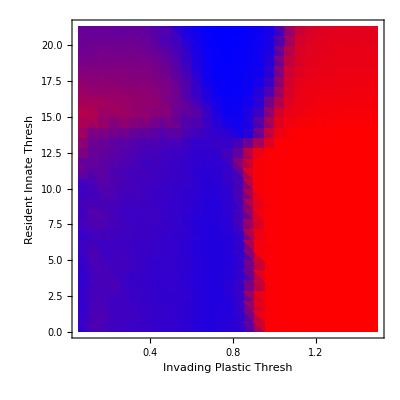

```mathematica
Tvafreq=ListDensityPlot[Flatten[frequencies,1], ColorFunction-> redtoblue,PlotLegends->None(*BarLegend[Automatic,LegendLabel->"Freq. of Plastic"]*)(*{{Red, Blue}, {0,5000}}, LegendLabel->"Donations"]*),PlotRange->All, FrameLabel -> {"Invading Plastic Thresh","Resident Innate Thresh"},(*AxesStyle->Directive[Black,Bold, 15],TicksStyle -> Directive[Black, Thick, 22,FontFamily->labelfont],*) FrameStyle->Directive[Black, 15, Thickness[.004]],LabelStyle -> {FontFamily->labelfont,Large, 15, Bold}]
```

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data"];
Export["fig4_frequencies_invadingplastic.txt", Flatten[N[frequencies]]];
SetDirectory[currentdir];
```

### Invading Innate

```mathematica
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/large_unprocessed_data/fig4b_residentplastic"];
```

```mathematica
Dims = {20};
CICs = Table[i, {i, 0.05, 1.5, 0.05}];
CFICs = Table[i*prediction[Dims[[1]]], {i, 0, 1.5, 0.05}];
```

```mathematica
generations = 5000;
selectionstrength=1;
phenotypemutation=1;
benefit=10;
cost = 1;
iterations = 1;
```

```mathematica
strategymutation = 0.000;
```

```mathematica
frequencies = Table[{CICs[[i]], CFICs[[j]], .5}, {i, 1, Length[CICs]},{j, 1, Length[CFICs]}];
donations = Table[{CICs[[i]], CFICs[[j]], 0}, {i, 1, Length[CICs]},{j, 1, Length[CFICs]}];
effectivethreshs = Table[{CICs[[i]], CFICs[[j]], 0}, {i, 1, Length[CICs]},{j, 1, Length[CFICs]}];
initialCfreq = Table[{CICs[[i]], CFICs[[j]], 0}, {i, 1, Length[CICs]},{j, 1, Length[CFICs]}];
```

```mathematica
For[i = 1, i ≤ Length[CICs], i++,
For[j = 1, j <= Length[CFICs], j++,
dat = Import["Context_STATISTICS_Dim020_Pop1000_Gen5000_B10.00_C1.00_PM1.0000_SM0.0000_ICthresh"<>ToString[NumberForm[CFICs[[j]], {6,5}]]<>"_ICscaler"<>ToString[NumberForm[CICs[[i]], {6,5}]]<>"_Tsigma0.50000_Ssigma0.01000_invadingscaler0.00000_iteration1"];
frequencies[[i]][[j]][[3]] = Mean[dat[[All,5]][[-2000;;]]];
donations[[i]][[j]][[3]] = Mean[dat[[All, 10]][[-2000;;]]];
effectivethreshs[[i]][[j]][[3]] = Mean[dat[[All, 11]][[-2000;;]]];
initialCfreq[[i]][[j]][[3]] = Mean[dat[[All, 5]][[2;;50]]];
]
]
```

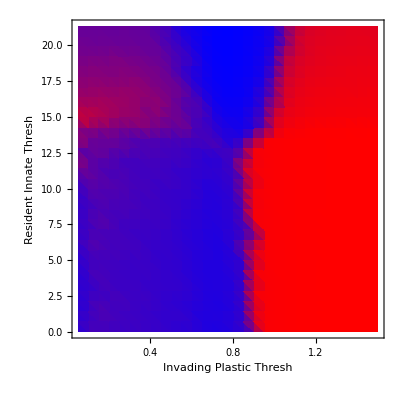

```mathematica
Tvafreq=ListDensityPlot[Flatten[frequencies,1], ColorFunction-> redtoblue,PlotLegends->None(*BarLegend[Automatic,LegendLabel->"Freq. of Plastic"]*)(*{{Red, Blue}, {0,5000}}, LegendLabel->"Donations"]*),PlotRange->All, FrameLabel -> {"Invading Plastic Thresh","Resident Innate Thresh"},(*AxesStyle->Directive[Black,Bold, 15],TicksStyle -> Directive[Black, Thick, 22,FontFamily->labelfont],*) FrameStyle->Directive[Black, 15, Thickness[.004]],LabelStyle -> {FontFamily->labelfont,Large, 15, Bold}]
```

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data"];
Export["fig4_frequencies_residentplastic.txt", Flatten[N[frequencies]]];
SetDirectory[currentdir];
```

### Evolving coordinates

```mathematica
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/large_unprocessed_data/fig4c_evolvingcoords"];
```

Procedure: 
Bin lists to sort coordinates : {scaler, thresh, time}.
Bin by scaler, then bin bins by thresh.
Now use time index to find the delta vectors. Most delta vectors are small (big transitions only happen when a uniform random mutant invades, which is rare). Only keep vectors that are large enough to change the bin designation.
Average these vectors.
Plot with List VectorPlot

```mathematica
CFICs = Table[i, {i, 1, 25, 2.5}];
CICs = Table[i, {i, .1, 1.5, .15}];
```

```mathematica
.71115/prediction[20]
```

0.05

```mathematica
learnedvinnatedata = Table[{}, {cic, 1, Length[CICs]},{cfic, 1, Length[CFICs]}];
scalersmatrix = Table[{}, {cic, 1, Length[CICs]},{cfic, 1, Length[CFICs]}];
threshmatrix=Table[{}, {cic, 1, Length[CICs]},{cfic, 1, Length[CFICs]}];
Cfreqmatrix = Table[{}, {cic, 1, Length[CICs]},{cfic, 1, Length[CFICs]}];
donationmatrix=Table[{}, {cic, 1, Length[CICs]},{cfic, 1, Length[CFICs]}];
For[cic = 1, cic ≤ Length[CICs],cic++,
For[cfic = 1, cfic ≤Length[CFICs],cfic++,

stat =Import["Context_STATISTICS_Dim020_Pop1000_Gen50000_B10.00_C1.00_PM1.0000_SM0.0010_ICthresh"<>ToString[NumberForm[CFICs[[cfic]], {6,5}]]<>"_ICscaler"<>ToString[NumberForm[CICs[[cic]], {6,5}]]<>"_Tsigma0.50000_Ssigma0.01000_invadingscaler0.00000_iteration1"];

times = Drop[stat[[All,1]],1];
threshs =Drop[stat[[All,14]],1];
scalers = Drop[stat[[All,15]],1];
Cfreq = Drop[stat[[All,5]],1];
donations = Drop[stat[[All,10]],1];

learnedvinnatedata[[cic]][[cfic]] = Transpose[{scalers, threshs, times}];
scalersmatrix[[cic]][[cfic]] = scalers;
threshmatrix[[cic]][[cfic]] = threshs;
Cfreqmatrix[[cic]][[cfic]] = Cfreq/1000;
donationmatrix[[cic]][[cfic]] = donations;
]
]
```

```mathematica
finalpts = Table[{learnedvinnatedata[[cic]][[cfic]][[499]][[1]],learnedvinnatedata[[cic]][[cfic]][[499]][[2]]}, {cic, 1, Length[CICs]}, {cfic, 1, Length[CFICs]}]
```

{{{0.850396,24.2375},{0.697402,17.5834},{0.790642,3.86148},{0.7684,16.8246},{0.87087,17.318},{0.81404,11.6463},{0.75078,5.95396},{0.694713,21.366},{0.79262,10.1488},{0.814529,12.8534}},{{0.749681,10.4201},{0.731152,23.0561},{0.872583,7.35041},{0.635309,17.6257},{0.928408,20.0342},{0.759272,10.0645},{0.606971,22.8836},{0.759442,16.049},{0.816409,11.0421},{0.729857,20.6644}},{{0.693344,23.5836},{0.585457,20.6547},{0.739624,15.4813},{0.718181,15.6624},{0.728619,23.9211},{0.768204,7.71824},{0.645701,21.4637},{0.685623,13.9691},{0.728771,21.4452},{0.696105,17.8399}},{{0.763503,6.29729},{0.854322,24.6526},{0.771063,14.3163},{0.735765,21.1867},{0.833335,7.62808},{0.603475,18.4387},{0.783917,24.5377},{0.526795,14.1202},{0.712511,20.1102},{0.713714,22.1182}},{{0.790979,0.5957},{0.766609,22.8465},{0.663418,22.264},{0.849641,13.5946},{0.818381,14.9238},{0.76468,10.01},{0.795739,5.48117},{0.788062,2.14059},{0.811233,4.65834},{0.755666,7.61584}},{{0.607906,17.2116},{0.762655,11.8367},{0.779579,24.0027},{0.699042,11.1748},{0.859816,18.6603},{0.715115,10.7503},{0.810927,24.6626},{0.774075,7.7871},{0.828947,24.7165},{0.79407,3.00177}},{{0.725551,9.41913},{0.773456,19.0647},{0.808146,7.47552},{0.717733,21.3017},{0.729393,0.847934},{0.820972,19.271},{0.798102,13.6132},{0.767314,12.5885},{0.697756,22.456},{0.601828,22.614}},{{0.730836,19.0238},{0.676951,7.01918},{0.841928,15.3625},{0.785551,1.24584},{0.617522,6.82708},{0.82297,14.3908},{0.858436,8.2535},{0.667877,13.7804},{0.613883,22.4101},{0.548065,9.02734}},{{0.773556,12.8302},{0.853972,14.0449},{0.764978,12.4511},{1.01414,16.7222},{0.693241,1.14258},{0.708656,0.937925},{0.605446,17.264},{0.680899,12.7061},{0.783673,20.1494},{0.81157,19.9992}},{{0.750976,9.921},{0.789883,11.524},{0.799458,18.0653},{0.718544,12.9078},{0.790158,11.5204},{0.80266,9.18012},{0.828679,16.0322},{0.838862,16.9351},{0.776535,8.79646},{0.644441,21.5678}}}

```mathematica
finalpts=Flatten[finalpts,1]
```

{{0.850396,24.2375},{0.697402,17.5834},{0.790642,3.86148},{0.7684,16.8246},{0.87087,17.318},{0.81404,11.6463},{0.75078,5.95396},{0.694713,21.366},{0.79262,10.1488},{0.814529,12.8534},{0.749681,10.4201},{0.731152,23.0561},{0.872583,7.35041},{0.635309,17.6257},{0.928408,20.0342},{0.759272,10.0645},{0.606971,22.8836},{0.759442,16.049},{0.816409,11.0421},{0.729857,20.6644},{0.693344,23.5836},{0.585457,20.6547},{0.739624,15.4813},{0.718181,15.6624},{0.728619,23.9211},{0.768204,7.71824},{0.645701,21.4637},{0.685623,13.9691},{0.728771,21.4452},{0.696105,17.8399},{0.763503,6.29729},{0.854322,24.6526},{0.771063,14.3163},{0.735765,21.1867},{0.833335,7.62808},{0.603475,18.4387},{0.783917,24.5377},{0.526795,14.1202},{0.712511,20.1102},{0.713714,22.1182},{0.790979,0.5957},{0.766609,22.8465},{0.663418,22.264},{0.849641,13.5946},{0.818381,14.9238},{0.76468,10.01},{0.795739,5.48117},{0.788062,2.14059},{0.811233,4.65834},{0.755666,7.61584},{0.607906,17.2116},{0.762655,11.8367},{0.779579,24.0027},{0.699042,11.1748},{0.859816,18.6603},{0.715115,10.7503},{0.810927,24.6626},{0.774075,7.7871},{0.828947,24.7165},{0.79407,3.00177},{0.725551,9.41913},{0.773456,19.0647},{0.808146,7.47552},{0.717733,21.3017},{0.729393,0.847934},{0.820972,19.271},{0.798102,13.6132},{0.767314,12.5885},{0.697756,22.456},{0.601828,22.614},{0.730836,19.0238},{0.676951,7.01918},{0.841928,15.3625},{0.785551,1.24584},{0.617522,6.82708},{0.82297,14.3908},{0.858436,8.2535},{0.667877,13.7804},{0.613883,22.4101},{0.548065,9.02734},{0.773556,12.8302},{0.853972,14.0449},{0.764978,12.4511},{1.01414,16.7222},{0.693241,1.14258},{0.708656,0.937925},{0.605446,17.264},{0.680899,12.7061},{0.783673,20.1494},{0.81157,19.9992},{0.750976,9.921},{0.789883,11.524},{0.799458,18.0653},{0.718544,12.9078},{0.790158,11.5204},{0.80266,9.18012},{0.828679,16.0322},{0.838862,16.9351},{0.776535,8.79646},{0.644441,21.5678}}

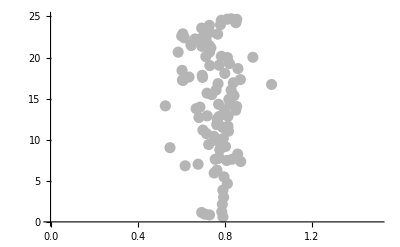

```mathematica
finalptsplot = ListPlot[finalpts, PlotStyle -> GrayLevel[0.71], BaseStyle->{PointSize[.02]}, PlotRange->{{0, 1.5}, {0, 25}}]
```

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data"];
Export["fig4_finalcoords.txt",N[Flatten[finalpts]]];
SetDirectory[currentdir];
```

```mathematica
colors= N[Table[Cfreqmatrix[[cic]][[cfic]][[499]],{cic, 1, Length[CICs]}, {cfic, 1, Length[CFICs]}]]
```

{{0.999,0.996,0.999,0.999,0.998,0.917,0.999,0.981,0.996,0.994},{0.992,0.996,0.744,0.982,1.,0.992,0.997,0.993,0.988,0.998},{0.998,0.981,0.982,0.993,0.995,0.978,0.999,0.996,0.999,0.991},{0.968,1.,0.995,1.,0.97,0.1,0.995,0.998,0.983,0.998},{0.976,0.999,0.999,0.992,0.998,0.971,0.966,0.987,0.998,0.993},{0.999,0.991,0.992,0.953,0.984,1.,0.993,0.994,0.995,0.976},{0.995,1.,0.993,0.998,0.988,0.998,0.996,0.99,0.999,0.91},{0.996,0.983,0.999,0.996,0.921,0.987,0.997,0.967,0.997,0.983},{0.995,0.997,0.98,0.997,0.985,0.987,0.99,0.991,0.999,0.997},{0.993,0.99,1.,0.996,0.997,0.997,0.999,0.994,0.989,0.997}}

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data"];
Export["fig4_finalcoords_frequencies.txt",N[Flatten[colors]]];
SetDirectory[currentdir];
```

```mathematica
maxscaler = Max[scalersmatrix];
maxthresh = Max[threshmatrix];
partitiongrid = 10;
partitionvectors = 20;
```

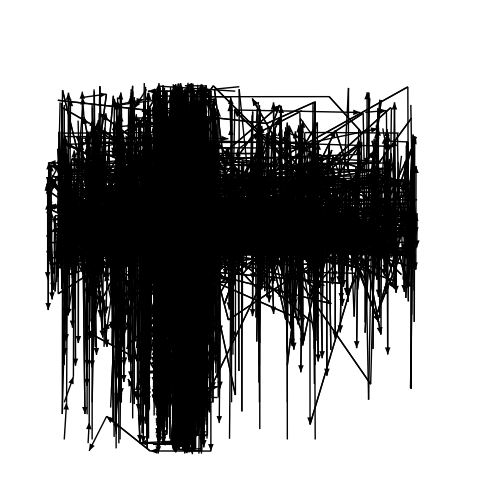

```mathematica
nonavarrows={};
vectors ={};

stransitiontimes = {};
ttransitiontimes = {};

For[cic = 1, cic ≤ Length[CICs],cic++,
For[cfic = 1, cfic ≤Length[CFICs],cfic++,

list=Sort[learnedvinnatedata[[cic]][[cfic]], #1[[1]]<#2[[1]]&];
partitions=BinCounts[list[[All,1]],maxscaler/partitiongrid];
binnedcoords=TakeList[list,partitions];

binnedsublists = {};
For[i = 1, i ≤ Length[binnedcoords], i++,
list=Sort[binnedcoords[[i]], #1[[2]]<#2[[2]]&];
If[list ≠ {},
partitions=BinCounts[list[[All,2]],maxthresh/partitiongrid];
AppendTo[binnedsublists,TakeList[list,partitions]];
];
];

droptime= Transpose[{learnedvinnatedata[[cic]][[cfic]][[All,1]], learnedvinnatedata[[cic]][[cfic]][[All,2]]}];
coordsineachstep=Partition[droptime, 2, 1];

stransitiontimes = {};
Table[If[EuclideanDistance[coordsineachstep[[i]][[1]][[1]],coordsineachstep[[i]][[2]][[1]]] ≥ maxscaler/partitionvectors,AppendTo[stransitiontimes,i],], {i, 1, Length[coordsineachstep]}];

ttransitiontimes = {};
Table[If[EuclideanDistance[coordsineachstep[[i]][[1]][[2]],coordsineachstep[[i]][[2]][[2]]] ≥ maxthresh/partitionvectors,AppendTo[ttransitiontimes,i],], {i, 1, Length[coordsineachstep]}];

arrows = Table[{Arrowheads[.02],Arrow[coordsineachstep[[i]]]},{i, Join[stransitiontimes,ttransitiontimes]}];
AppendTo[nonavarrows, arrows];
AppendTo[vectors,Table[coordsineachstep[[i]],{i, Join[stransitiontimes,ttransitiontimes]}]];
];
];

Graphics[nonavarrows, PlotRange->{{0,maxscaler*1.1},{0,maxthresh*1.1}}, AspectRatio->1, ImageSize->500]
```

```mathematica
allvectors=Flatten[vectors,1];
sortbyscaler = Sort[allvectors, #1[[1]][[1]]<#2[[1]][[1]]&];
partitionss=BinCounts[Transpose[sortbyscaler[[All]]][[1]][[All,1]], {0, maxscaler,maxscaler/partitiongrid}];
binnedcoords=TakeList[sortbyscaler,partitionss];
```

```mathematica
totalbinnedsublists = {};
For[i = 1, i ≤ Length[binnedcoords],i++,
sortbythresh = Sort[binnedcoords[[i]], #1[[1]][[2]]<#2[[1]][[2]]&];
If[sortbythresh ≠ {},
partitionst=BinCounts[Transpose[sortbythresh[[All]]][[1]][[All,2]], {0, maxthresh,maxthresh/partitiongrid}];
AppendTo[totalbinnedsublists, TakeList[sortbythresh, partitionst]];
]
];
```

```mathematica
averaged=Table[Mean[totalbinnedsublists[[i]][[j]]],{i, 1,partitiongrid},  {j, 1, partitiongrid}];
dropnothings = {};
biggestdeltas = 0;
biggestdeltat=0;
For[i = 1, i ≤ partitiongrid, i++,
For[j = 1, j ≤ partitiongrid,j++,

If[Length[averaged[[i]][[j]]]≠  1,
deltas = {{averaged[[i]][[j]][[2]][[1]]-averaged[[i]][[j]][[1]][[1]]},{averaged[[i]][[j]][[2]][[2]]-averaged[[i]][[j]][[1]][[2]]}};

If[deltas[[1]][[1]]>biggestdeltas,biggestdeltas= deltas[[1]]];
If[deltas[[2]][[1]]>biggestdeltat,biggestdeltat= deltas[[2]]];

AppendTo[dropnothings, averaged[[i]][[j]]];
];
];
];
```

```mathematica
recenterdropnothings = {};
For[i = 1, i ≤ partitiongrid, i++,
For[j = 1, j ≤ partitiongrid,j++,
If[Length[averaged[[i]][[j]]]≠  1,
AppendTo[recenterdropnothings, {{i*maxscaler/partitiongrid, j*maxthresh/partitiongrid}, Flatten[{i*maxscaler/partitiongrid, j*maxthresh/partitiongrid}+{{averaged[[i]][[j]][[2]][[1]]-averaged[[i]][[j]][[1]][[1]]}, {averaged[[i]][[j]][[2]][[2]]-averaged[[i]][[j]][[1]][[2]]}}]}];
];
];
];
```

```mathematica
davarrows = Table[{Arrowheads[.015],Arrow[recenterdropnothings[[i]]]}, {i, 1, Length[recenterdropnothings]}];
arrowplot=Graphics[davarrows, PlotRange->{{0,maxscaler*1.25},{0,30}}, AspectRatio->1, ImageSize->500, Axes->True];
lines = Graphics[{Dashed, Red,Line[{{0,prediction[20]}, {maxthresh*1.25,prediction[20]}}]},PlotRange->{{0,maxscaler*1.25},{0,maxthresh*1.25}},AspectRatio->1, ImageSize->500, Axes->True];
```

```mathematica
arrowgraphic=-Graphics-;
```

```mathematica
magnitudes = Table[EuclideanDistance[recenterdropnothings[[i]][[1]], recenterdropnothings[[i]][[2]]],{i, 1, Length[recenterdropnothings]}];
angle2=Table[0, {i, 1, Length[recenterdropnothings]}];
deltav=Table[recenterdropnothings[[i]][[2]]-recenterdropnothings[[i]][[1]], {i, 1, Length[recenterdropnothings]}];
deltav[[All,1]] *=10;
```

```mathematica
For[i = 1, i<= Length[recenterdropnothings],i++,
If[deltav[[i]][[1]] < 0,
If[deltav[[i]][[2]]<0, angle2[[i]]=Pi+VectorAngle[{1,0}, Abs[deltav[[i]]]],
angle2[[i]]=Pi-VectorAngle[{1,0}, Abs[deltav[[i]]]];
],
];

If[deltav[[i]][[1]] > 0, 
If[deltav[[i]][[2]]<0, angle2[[i]]=2*Pi-VectorAngle[{1,0}, Abs[deltav[[i]]]],
angle2[[i]]=VectorAngle[{1,0}, Abs[deltav[[i]]]]
],
]
]
biggest=Max[magnitudes];
```

```mathematica
arrows=Table[Graphics[Rotate[arrowgraphic,angle2[[i]]],ImageSize->magnitudes[[i]]*30/biggest+15] ,{i, 1, Length[recenterdropnothings]}];
origins = Table[recenterdropnothings[[i]][[1]], {i, 1, Length[recenterdropnothings]}];
origins=Partition[origins,1];
```

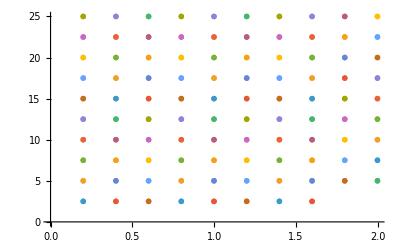

```mathematica
arrowplot=ListPlot[origins, PlotMarkers->arrows]
```

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data"];
Export["fig4_evolvingcoords_angles.txt", Flatten[N[angle2]]];
Export["fig4_evolvingcoords_magnitudes.txt", Flatten[N[magnitudes]]];
Export["fig4_evolvingcoords_arroworigins.txt", Flatten[N[recenterdropnothings]]];
SetDirectory[currentdir];
```

## Figure 5: 2-cluster regime

```mathematica
(*SetDirectory["~/Desktop/oct8"];*)
```

```mathematica
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/large_unprocessed_data/fig5a_intraplastic"]
```

/Users/linneabavik/Desktop/altruism_2_repo/large_unprocessed_data/fig5a_intraplastic

```mathematica
Clear[x];
prediction[x_]:=-6.367767314992545+4.6042335007240975 √x;
```

```mathematica
redtoblue[z_]:= Blend[{RGBColor[1,0,0], RGBColor[0,0,1]}, z];
bluetored[z_] := Blend[{RGBColor[0,0,1], RGBColor[1,0,0]}, z];
```

```mathematica
CICs = Table[i, {i, 0.05, 1.3,.3}]
its = 1;
```

{0.05,0.35,0.65,0.95,1.25}

```mathematica
flatphenova={};
```

```mathematica
statdata=Import["Context_STATISTICS_Dim020_Pop1000_Gen10000000_B10.00_C1.00_PM1.0000_SM0.0010_ICthresh1000.00000_ICscaler0.65000_Tsigma0.50000_Ssigma0.01000_invadingscaler0.00000_iteration1"];
```

```mathematica
phenova={};
phenovscaler =Transpose[{Drop[statdata[[All,15]],1], Drop[statdata[[All,8]],1]}];
AppendTo[phenova,Transpose[{Drop[statdata[[All,8]],1],Drop[statdata[[All,15]],1]}]];
```

```mathematica
AppendTo[flatphenova,Flatten[phenova,1]];
```

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data"];
Export["fig5_flatphenova.csv",Flatten[flatphenova,1]]
```

fig5_flatphenova.csv

```mathematica
threshs = Transpose[{Drop[statdata[[All,8]],1],Drop[statdata[[All,11]],1]}]
```

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data"];
Export["fig5_threshsused.csv",Flatten[threshs,1]]
```

fig5_threshsused.csv

## Supplement Figure : Robustness

```mathematica
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/large_unprocessed_data/supplement_fig"];
```

```mathematica
ptsontop = {{1.2, 2.2, 3.2}, {4.5, 5.5, 6.5}, {7.8, 8.8, 9.8}};
```

### b/c

```mathematica
scalings={100,100,100};
```

```mathematica
benefit={5.0,10.0,20.0};
```

```mathematica
iterations =5;
```

```mathematica
strategymutation={0.001};
```

```mathematica
Dims = {20};
```

```mathematica
popsizes = {500,1000,2000};
```

```mathematica
meanfreq=Table[{}, {j,1,Length[popsizes]},{i, 1, Length[benefit]}];
meanfreqnum=Table[{},{j,1,Length[popsizes]}, {i, 1, Length[benefit]}];
```

```mathematica
totalfreqs=Table[{}, {j,1,Length[popsizes]},{i, 1, Length[benefit]},{k, 1, 5}];
allpts={};
```

```mathematica
popsize=500;
```

```mathematica
For[j=1, j<= Length[popsizes],j++,
scalerfreq=Table[{}, {i, 1, Length[benefit]},{it, 1, iterations}];
For[i=1, i <= Length[benefit],i++,
For[it = 1,it<=5, it++,
stat =Import["Context_STATISTICS_Dim"<>IntegerString[Dims[[1]], 10, 3]<>"_Pop"<>ToString[popsizes[[j]]]<>"_Gen50000_B"<>ToString[NumberForm[benefit[[i]], {4,2}]]<>"_C1.00_PM1.0000_SM"<>ToString[NumberForm[strategymutation[[1]], {6,4}]]<>"_ICthresh"<>ToString[NumberForm[prediction[Dims[[1]]], {6,5}]]<>"_ICscaler0.80000_Tsigma0.50000_Ssigma0.01000_invadingscaler0.00000_iteration"<>ToString[it]];
times = Drop[stat[[All,1]],1];
scalerfreq[[i]][[it]] = Drop[stat[[All,5]],1];
(*totalfreqs[[j]][[i]][[it]] = Mean[Drop[stat[[All,5]],1][[-100;;]]];*)
(*AppendTo[allpts,{ptsontop[[j]][[i]],Mean[Drop[stat[[All,5]],1][[-50000/scalings[[j]];;]]]/popsizes[[j]]}];*)
];
]
]
```

```mathematica
For[j=1, j<= Length[popsizes],j++,
scalerfreq=Table[{}, {i, 1, Length[benefit]},{it, 1, iterations}];
For[i=1, i <= Length[benefit],i++,
For[it = 1,it<=5, it++,
stat =Import["Context_STATISTICS_Dim"<>IntegerString[Dims[[1]], 10, 3]<>"_Pop"<>ToString[popsizes[[j]]]<>"_Gen50000_B"<>ToString[NumberForm[benefit[[i]], {4,2}]]<>"_C1.00_PM1.0000_SM"<>ToString[NumberForm[strategymutation[[1]], {6,4}]]<>"_ICthresh"<>ToString[NumberForm[prediction[Dims[[1]]], {6,5}]]<>"_ICscaler0.80000_Tsigma0.50000_Ssigma0.01000_invadingscaler0.00000_iteration"<>ToString[it]];
times = Drop[stat[[All,1]],1];
scalerfreq[[i]][[it]] = Drop[stat[[All,5]],1];
totalfreqs[[j]][[i]][[it]] = Mean[Drop[stat[[All,5]],1][[-100;;]]];
AppendTo[allpts,{ptsontop[[j]][[i]],Mean[Drop[stat[[All,5]],1][[-50000/scalings[[j]];;]]]/popsizes[[j]]}];
];
meanfreq[[j]][[i]] = Transpose[{times,Mean[scalerfreq[[i]]]}];
meanfreqnum[[j]][[i]] = N[Mean[Mean[scalerfreq[[i]]][[-50000/scalings[[j]];;]]]/popsizes[[j]]];
]
]
```

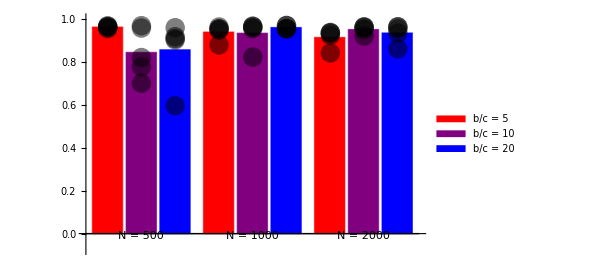

```mathematica
newbcplot=Show[BarChart[meanfreqnum,PlotRange->{All,{-.075, 1}},ChartLegends->{Style["b/c = 5",17.5],Style["b/c = 10",17.5],Style["b/c = 20",17.5]}, ChartLabels->{{"N = 500","N = 1000","N = 2000"},None},ChartStyle->{Red, Purple, Blue},AxesStyle->{{Bold,Black,15},{Bold,Black,15}},AxesLabel->{None,None},ImageSize->450,ImagePadding-> {{100, 20}, {10, 14}},Epilog->Text[Style[C,27,Bold,FontFamily-> labelfont],Offset[{0,0},{-1.,1}]]],ListPlot[allpts, PlotStyle->{Black,Opacity[.5]}, PlotMarkers->{"●",20}]]
```

```mathematica
(*newbcplot=Show[bcplot, ListPlot[allpts, PlotStyle->{Black,Opacity[.5]}, PlotMarkers->{"●",20}]]*)
```

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data"];
Export["supplement1_meanfreqnm_bc.txt", Flatten[N[meanfreqnum]]];
Export["supplement1_allpts_bc.txt", Flatten[N[allpts]]];
SetDirectory[currentdir];
```

### SM

```mathematica
scalings={100,100,100}
```

{100,100,100}

```mathematica
benefit={10.0};
```

```mathematica
strategymutation={0.0001,0.001,0.01};
```

```mathematica
Dims = {20};
```

```mathematica
popsizes = {500,1000,2000};
```

```mathematica
meanfreq=Table[{}, {j,1,Length[popsizes]},{i, 1, Length[strategymutation]}];
meanfreqnum=Table[{},{j,1,Length[popsizes]}, {i, 1, Length[strategymutation]}];
```

```mathematica
totalfreqs=Table[{}, {j,1,Length[popsizes]},{i, 1, Length[strategymutation]},{k, 1, 5}];
allpts={};
```

```mathematica
popsize=500;
```

```mathematica
For[j=1, j<= Length[popsizes],j++,
scalerfreq=Table[{}, {i, 1, Length[strategymutation]},{it, 1, iterations}];
For[i=1, i <= Length[strategymutation],i++,
For[it = 1,it<=5, it++,
stat =Import["Context_STATISTICS_Dim"<>IntegerString[Dims[[1]], 10, 3]<>"_Pop"<>ToString[popsizes[[j]]]<>"_Gen50000_B"<>ToString[NumberForm[benefit[[1]], {4,2}]]<>"_C1.00_PM1.0000_SM"<>ToString[NumberForm[strategymutation[[i]], {6,4}]]<>"_ICthresh"<>ToString[NumberForm[prediction[Dims[[1]]], {6,5}]]<>"_ICscaler0.80000_Tsigma0.50000_Ssigma0.01000_invadingscaler0.00000_iteration"<>ToString[it]];
times = Drop[stat[[All,1]],1];
scalerfreq[[i]][[it]] = Drop[stat[[All,5]],1];
totalfreqs[[j]][[i]][[it]] = Mean[Drop[stat[[All,5]],1][[-100;;]]];
AppendTo[allpts,{ptsontop[[j]][[i]],Mean[Drop[stat[[All,5]],1][[-50000/scalings[[j]];;]]]/popsizes[[j]]}];
];
meanfreq[[j]][[i]] = Transpose[{times,Mean[scalerfreq[[i]]]}];
meanfreqnum[[j]][[i]] = N[Mean[Mean[scalerfreq[[i]]][[-50000/scalings[[j]];;]]]/popsizes[[j]]];
]
]
```

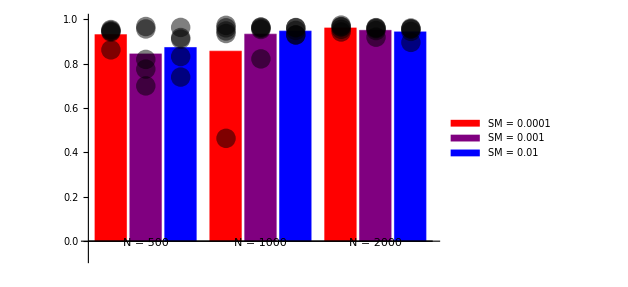

```mathematica
smplot=Show[BarChart[meanfreqnum,PlotRange->{All,{-.075, 1}},ChartLegends->{Style["SM = 0.0001",17.5],Style["SM = 0.001",17.5],Style["SM = 0.01",17.5]},ChartLabels->{{"N = 500","N = 1000","N = 2000"},None},ChartStyle->{Red, Purple, Blue},AxesStyle->{{Bold,Black,15},{Bold,Black,15}},(*AxesLabel->{None,"Frequency"},*)(*ImagePadding->30,*)ImagePadding-> {{130, 20}, {10, 12}},ImageSize->465,Epilog->Text[Style[A,27,Bold,FontFamily-> labelfont],Offset[{0,0},{-1.,1}]]],ListPlot[allpts, PlotStyle->{Black,Opacity[.5]}, PlotMarkers->{"●",20}]]
```

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data"];
Export["supplement1_meanfreqnm_SM.txt", Flatten[N[meanfreqnum]]];
Export["supplement1_allpts_SM.txt", Flatten[N[allpts]]];
SetDirectory[currentdir];
```

### Dimension

```mathematica
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/large_unprocessed_data/supplement_fig_dims"];
```

```mathematica
scalings={100,100,100}
```

{100,100,100}

```mathematica
benefit={10.0};
```

```mathematica
strategymutation={0.001};
```

```mathematica
Dims = {5,20,40};
```

```mathematica
popsizes = {500,1000,2000};
```

```mathematica
meanfreq=Table[{}, {j,1,Length[popsizes]},{i, 1, Length[Dims]}];
meanfreqnum=Table[{},{j,1,Length[popsizes]}, {i, 1, Length[Dims]}];
```

```mathematica
totalfreqs=Table[{}, {j,1,Length[popsizes]},{i, 1, Length[Dims]},{k, 1, 5}];
allpts={};
```

```mathematica
For[j=1, j<= Length[popsizes],j++,
scalerfreq=Table[{}, {i, 1, Length[Dims]},{it, 1, iterations}];
For[i=1, i <= Length[Dims],i++,
For[it = 1,it<=5, it++,
stat =Import["Context_STATISTICS_Dim"<>IntegerString[Dims[[i]], 10, 3]<>"_Pop"<>ToString[popsizes[[j]]]<>"_Gen50000_B"<>ToString[NumberForm[benefit[[1]], {4,2}]]<>"_C1.00_PM1.0000_SM"<>ToString[NumberForm[strategymutation[[1]], {6,4}]]<>"_ICthresh"<>ToString[NumberForm[prediction[Dims[[i]]], {6,5}]]<>"_ICscaler0.80000_Tsigma0.50000_Ssigma0.01000_invadingscaler0.00000_iteration"<>ToString[it]];
times = Drop[stat[[All,1]],1];
scalerfreq[[i]][[it]] = Drop[stat[[All,5]],1];
totalfreqs[[j]][[i]][[it]] = Mean[Drop[stat[[All,5]],1][[-100;;]]];
AppendTo[allpts,{ptsontop[[j]][[i]],Mean[Drop[stat[[All,5]],1][[-50000/scalings[[j]];;]]]/popsizes[[j]]}];
];
meanfreq[[j]][[i]] = Transpose[{times,Mean[scalerfreq[[i]]]}];
meanfreqnum[[j]][[i]] = N[Mean[Mean[scalerfreq[[i]]][[-50000/scalings[[j]];;]]]/popsizes[[j]]];
]
]
```

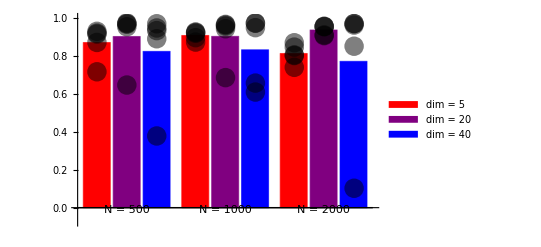
-Graphics-Plastic Frequency

```mathematica
newdimplot=Labeled[Show[BarChart[meanfreqnum,PlotRange->{All,{-.075, 1}},ChartLegends->{Style["dim = 5",17.5],Style["dim = 20",17.5],Style["dim = 40",17.5]}, ChartLabels->{{"N = 500","N = 1000","N = 2000"},None},ChartStyle->{Red, Purple, Blue},AxesStyle->{{Bold,Black,15},{Bold,Black,15}},AxesLabel->{None,None},ImageSize->400,ImagePadding-> {{65, 20}, {22, 22}},Epilog->Text[Style[B,27,Bold,FontFamily-> labelfont],Offset[{0,0},{-1.,1}]]],ListPlot[allpts, PlotStyle->{Black,Opacity[.5]}, PlotMarkers->{"●",20}]],"Plastic Frequency", {{Left, Center}}, RotateLabel->True,LabelStyle -> {FontFamily->labelfont,Large, 28, Bold}]
```

```mathematica
currentdir=Directory[];
SetDirectory[ToString[pathtodirectory]<>"altruism_2_repo/data"];
Export["supplement1_meanfreqnm_dim.txt", Flatten[N[meanfreqnum]]];
Export["supplement1_allpts_dim.txt", Flatten[N[allpts]]];
SetDirectory[currentdir];
```

```mathematica
robustplot=GraphicsColumn[{smplot,newdimplot,newbcplot},Spacings->0, ImageSize->650]
```

-Graphics-

```mathematica
SetDirectory["~/Desktop"];
 Export["robustplot.pdf", robustplot]
```

robustplot.pdf

```mathematica
(*Export["robustplot.png", robustplot]*)
```